```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κ>3/2,θ>0};

FullSimplify[Solve[n==A*Integrate[4*Pi*v^2*(1+v^2/(κ*θ^2))^(-(κ+1)),{v,0,Infinity},Assumptions->assumps],A,Assumptions->assumps],assumps]
```

{{A→(n Gamma[κ])/(π^(3/2) θ^3 √κ Gamma[-1/2+κ])}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];
assumps={κ>3/2,Tpar>0,Tperp>0,m>0};

FullSimplify[Solve[n==A*2*Pi*Integrate[vperp*(1+vpar^2/(κ*θpar^2)+ vperp^2/(κ*θperp^2))^(-(κ+1)),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],A,Assumptions->assumps],assumps]
```

{{A→(m^(3/2) n Gamma[κ])/(2 √2 π^(3/2) Tperp √(Tpar κ) Gamma[-1/2+κ])}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={m>0,T>0,n>0};

FullSimplify[Solve[n==A*Integrate[4*Pi*v^2*Exp[-m*v^2/(2*T)],{v,0,Infinity},Assumptions->assumps],A,Assumptions->assumps],assumps]
```

{{A→(n (m/T)^(3/2))/(2 √2 π^(3/2))}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={m>0,Tpar>0,n>0,Tperp>0};

FullSimplify[Solve[n==A*Integrate[2*Pi*vperp*Exp[-m*vpar^2/(2*Tpar)]*Exp[-m*vperp^2/(2*Tperp)],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],A,Assumptions->assumps],assumps]
```

{{A→(m^(3/2) n)/(2 √2 π^(3/2) √Tpar Tperp)}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];
assumps={κ>3/2,Tpar>0,Tperp>0,m>0};

FullSimplify[Solve[n==A*2*Pi*Integrate[vperp*((1+ vperp^2/(κ*θperp^2))^(-(κ+1)))*(1+vpar^2/(κ*θpar^2))^(-(κ+1)),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],A,Assumptions->assumps],assumps]
```

{{A→(m^(3/2) n Gamma[1+κ])/(2 √2 π^(3/2) Tperp √(Tpar κ) Gamma[1/2+κ])}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κ>=1,Tpar>0,Tperp>0,m>0};

FullSimplify[Solve[n==A*2*Pi*Integrate[vperp*
,{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],A,Assumptions->assumps],assumps]
```

{{A→(m^(3/2) n)/(2 √2 π^(3/2) √Tpar Tperp)}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"] 
θperp=Sqrt[2*Tperp/m];
θpar=Sqrt[2*Tpar/m];
assumps={κperp>=1,κpar>=1/2,Tpar>0,Tperp>0,m>0};

FullSimplify[Solve[n==A*2*Pi*Integrate[vperp*((1+ vperp^2/(κperp*θperp^2))^(-(κperp+1)))*(1+vpar^2/(κpar*θpar^2))^(-(κpar+1)),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],A,Assumptions->assumps],assumps]
```

{{A→(m^(3/2) n Gamma[1+κpar])/(2 √2 π^(3/2) Tperp √(Tpar κpar) Gamma[1/2+κpar])}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

C0=(n0 Gamma[κ])/(π^(3/2) θpar0 θperp0^2 √κ Gamma[-1/2+κ]);(*(m^(3/2) n Gamma[κ])/(2 √2 π^(3/2) Tperp √(Tpar κ) Gamma[-1/2+κ])*)

twiceΔPEoverm = -2*G*M*(1/r - 1/r0)-Ω^2*(ρ^2-ρ0^2)+2*q*ϕ/m;
assumps={κ>3/2,θpar0>0,θperp0>0, B>0,B0>0,A0>0,ϕ∈Reals,q∈Reals,m>0,M>0,r>0,r0>0,G>0,Ω>0,ρ>0,ρ0>0};

FullSimplify[C0*2*Pi*Integrate[vperp*(1+vpar^2/(κ*θpar0^2)+ ((vperp^2)*(A0+(1-A0)*B0/B))/(κ*θperp0^2)+twiceΔPEoverm/(κ*θpar0^2))^(-(κ+1)),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],assumps]
```

ConditionalExpression[(B n0 (1+(2 G M (-1/r+1/r0)+(2 q ϕ)/m+(-ρ^2+ρ0^2) Ω^2)/(θpar0^2 κ))^-κ)/((A0 (B-B0)+B0) θpar0 √((m r r0 κ)/(2 G m M (r-r0)+r r0 (m θpar0^2 κ+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2)))), r (2 G M+r0 θpar0^2 κ+r0 (-ρ^2+ρ0^2) Ω^2)≥2 G M r0&&2 G m M (r-r0)+r r0 (m θpar0^2 κ+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2)>0]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

C0=(m^(3/2) n0)/(2 √2 π^(3/2) √Tpar0 Tperp0);

twiceΔPEoverm = -2*G*M*(1/r - 1/r0)-Ω^2*(ρ^2-ρ0^2)+2*q*ϕ/m;
assumps={Tpar0>0,Tperp0>0, B>0,B0>0,A0>0,ϕ∈Reals,q∈Reals,m>0,M>0,r>0,r0>0,G>0,Ω>0,ρ>0,ρ0>0};

FullSimplify[C0*2*Pi*Exp[-m*twiceΔPEoverm/(2*Tpar0)]*Integrate[vperp*Exp[-m*vpar^2/(2*Tpar0)]*Exp[-m*(vperp^2*(A0+(1-A0)*B0/B))/(2*Tperp0)],{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],assumps]
```

(B ⅇ^(-(m (2 G M (-1/r+1/r0)+(2 q ϕ)/m+(-ρ^2+ρ0^2) Ω^2))/(2 Tpar0)) n0)/(A0 (B-B0)+B0)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
twiceΔPEoverm = -2*G*M*(1/r - 1/r0)-Ω^2*(ρ^2-ρ0^2)+2*q*ϕ/m;
assumps1={κ>3/2,Tpar0>0,Tperp0>0, B>0,B0>0,A0>0,ϕ∈Reals,q∈Reals,m>0,M>0,r>0,r0>0,G>0,Ω>0,ρ>0,ρ0>0,M>m,vperp>=0};
C0=(m^(3/2) n0 Gamma[1+κ])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κ) Gamma[1/2+κ]);


fac=FullSimplify[vperp*((1+ (m*vperp^2*B0)/(B*2*κ*Tperp0))^(-(κ+1)))*Integrate[(1+1/(κ*2*Tpar0)m*(vpar^2+vperp^2*(1-B0/B)+twiceΔPEoverm))^(-(κ+1)),{vpar,-Infinity,Infinity},Assumptions->assumps1],assumps1]
```

ConditionalExpression[(4^(1+κ) √π Tpar0 vperp κ (B r r0 Tpar0 κ)^κ ((B Tperp0 κ)/(B0 m vperp^2+2 B Tperp0 κ))^(1+κ) √((B m r r0)/(2 B G m M (r-r0)-B0 m r r0 vperp^2+B r r0 (m vperp^2+2 Tpar0 κ+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2))) (2 B G m M (r-r0)-B0 m r r0 vperp^2+B r r0 (m vperp^2+2 Tpar0 κ+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2))^-κ Gamma[1/2+κ])/(m Gamma[1+κ]), ]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
twiceΔPEoverm = -2*G*M*(1/r - 1/r0)-Ω^2*(ρ^2-ρ0^2)+2*q*ϕ/m;
assumps1={κ>3/2,Tpar0>0,Tperp0>0, B>0,B0>0,ϕ∈Reals,q∈Reals,m>0,M>0,r>0,r0>0,G>0,Ω>0,ρ>0,ρ0>0,M>m,vpar∈Reals};
C0=(m^(3/2) n0 Gamma[1+κ])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κ) Gamma[1/2+κ]);


fac=FullSimplify[Integrate[vperp*((1+ (m*vperp^2*B0)/(B*2*κ*Tperp0))^(-(κ+1)))*(1+1/(κ*2*Tpar0)m*(vpar^2+vperp^2*(1-B0/B)+twiceΔPEoverm))^(-(κ+1)),{vperp,0,Infinity},Assumptions->assumps1],assumps1]
```

ConditionalExpression[1/((B-B0) m)2^κ B Tpar0 (r r0 Tpar0 κ)^κ (2 G m M (r-r0)+r r0 (m vpar^2+2 Tpar0 κ+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2))^-κ (-1/Gamma[1+κ]2^κ B0^κ √π κ (((B-B0) r r0 Tperp0 κ)/(2 G m M (r-r0)+r r0 (m vpar^2+2 Tpar0 κ+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2)))^-κ (1-(B0 (2 G m M (r-r0)+r r0 (m vpar^2+2 Tpar0 κ+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2)))/(2 (B-B0) r r0 Tperp0 κ))^(-1-2 κ) Csc[π κ] Gamma[1/2+κ]+Hypergeometric2F1[1,1+κ,1-κ,(B0 (2 G m M (r-r0)+r r0 (m vpar^2+2 Tpar0 κ+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2)))/(2 (B-B0) r r0 Tperp0 κ)]), ]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

assumps={κ>3/2,Tpar0>0,Tperp0>0, B>0,B0>0,ϕ∈Reals,q∈Reals,m>0,M>0,r>0,r0>0,G>0,Ω>0,ρ>0,ρ0>0,M>m};
C0=(m^(3/2) n0 Gamma[1+κ])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κ) Gamma[1/2+κ]);

(*(m^(3/2) n Gamma[1+κ])/(2 √2 π^(3/2) Tperp √(Tpar κ) Gamma[1/2+κ])*)
fac=Integrate[(4^(1+κ) √π Tpar0 vperp κ (B r r0 Tpar0 κ)^κ ((B Tperp0 κ)/(B0 m vperp^2+2 B Tperp0 κ))^(1+κ) √((B m r r0)/(2 B G m M (r-r0)-B0 m r r0 vperp^2+B r r0 (m vperp^2+2 Tpar0 κ+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2))) (2 B G m M (r-r0)-B0 m r r0 vperp^2+B r r0 (m vperp^2+2 Tpar0 κ+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2))^-κ Gamma[1/2+κ])/(m Gamma[1+κ]),{vperp,0,Infinity},Assumptions->assumps]

(*FullSimplify[C0*2*Pi*fac,assumps]*)
```

Integrate[1/(m Gamma[1+κ])4^(1+κ) √π Tpar0 vperp κ (B r r0 Tpar0 κ)^κ ((B Tperp0 κ)/(B0 m vperp^2+2 B Tperp0 κ))^(1+κ) √((B m r r0)/(2 B G m M (r-r0)-B0 m r r0 vperp^2+B r r0 (m vperp^2+2 Tpar0 κ+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2))) (2 B G m M (r-r0)-B0 m r r0 vperp^2+B r r0 (m vperp^2+2 Tpar0 κ+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2))^-κ Gamma[1/2+κ],{vperp,0,∞},Assumptions→{κ>3/2,Tpar0>0,Tperp0>0,B>0,B0>0,ϕ∈ℝ,q∈ℝ,m>0,M>0,r>0,r0>0,G>0,Ω>0,ρ>0,ρ0>0,M>m}]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

assumps={κ>3/2,Tpar0>0,Tperp0>0, B>0,B0>0,ϕ∈Reals,q∈Reals,m>0,M>0,r>0,r0>0,G>0,Ω>0,ρ>0,ρ0>0,M>m};
C0=(m^(3/2) n0 Gamma[1+κ])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κ) Gamma[1/2+κ]);

(*(m^(3/2) n Gamma[1+κ])/(2 √2 π^(3/2) Tperp √(Tpar κ) Gamma[1/2+κ])*)
fac=Integrate[1/((B-B0) m)2^κ B Tpar0 (r r0 Tpar0 κ)^κ (2 G m M (r-r0)+r r0 (m vpar^2+2 Tpar0 κ+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2))^-κ (-1/Gamma[1+κ] 2^κ B0^κ √π κ (((B-B0) r r0 Tperp0 κ)/(2 G m M (r-r0)+r r0 (m vpar^2+2 Tpar0 κ+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2)))^-κ (1-(B0 (2 G m M (r-r0)+r r0 (m vpar^2+2 Tpar0 κ+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2)))/(2 (B-B0) r r0 Tperp0 κ))^(-1-2 κ) Csc[π κ] Gamma[1/2+κ]+Hypergeometric2F1[1,1+κ,1-κ,(B0 (2 G m M (r-r0)+r r0 (m vpar^2+2 Tpar0 κ+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2)))/(2 (B-B0) r r0 Tperp0 κ)]),{vpar,-Infinity,Infinity},Assumptions->assumps]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
twiceΔPEoverm = -2*G*M*(1/r - 1/r0)-Ω^2*(ρ^2-ρ0^2)+2*q*ϕ/m;
C0 =(m^(3/2) n0)/(2 √2 π^(3/2) √Tpar0 Tperp0);



assumps1={κ>3/2,Tpar0>0,Tperp0>0,twiceΔPEoverm∈Reals, B>0,B0>0,A0>0,ϕ∈Reals,q∈Reals,m>0,M>0,r>0,r0>0,G>0,Ω>0,ρ>0,ρ0>0, M>m};
assumps2={κ>3/2,Tpar0>0,Tperp0>0, B>0,B0>0,m>0};

fac1=Integrate[Exp[-m*vpar^2/(2*Tpar0)],{vpar,-Infinity,Infinity},Assumptions->assumps1]

Integrate[Exp[-u]*(1+D u)^(-1-k),{u,0,Infinity}]

fac2=Exp[κ*Tperp0/Tpar0*(B/B0-1)]*κ*Tperp0/Tpar0*(B/B0-1)*ExpIntegralE[κ+1,κ*Tperp0/Tpar0*(B/B0-1)] (*See notes and Output above*)(*Integrate[vperp*Exp[-m*(vperp^2*(1-B0/B))/(2*Tpar0)]*(1+(m*B0*vperp^2)/(B*κ*2*Tperp0))^(-(κ+1)),{vperp,0,Infinity},Assumptions->assumps2]*)

FullSimplify[C0*2*Pi*Exp[-m*twiceΔPEoverm/(2*Tpar0)]*fac1*fac2,assumps1]
```

√(2 π) √(Tpar0/m)

ConditionalExpression[(ⅇ^(1/D) ExpIntegralE[1+k,1/D])/D, Im[D]≠0||Re[D]>0]

1/Tpar0(-1+B/B0) ⅇ^(((-1+B/B0) Tperp0 κ)/Tpar0) Tperp0 κ ExpIntegralE[1+κ,((-1+B/B0) Tperp0 κ)/Tpar0]

1/(B0 Tpar0)(B-B0) ⅇ^(-(2 G m M (-1/r+1/r0)+(2 (-B+B0) Tperp0 κ)/B0+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2)/(2 Tpar0)) m n0 κ ExpIntegralE[1+κ,((-1+B/B0) Tperp0 κ)/Tpar0]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
twiceΔPEoverm = -2*G*M*(1/r - 1/r0)-Ω^2*(ρ^2-ρ0^2)+2*q*ϕ/m;
assumps={κ>3/2,θpar0>0,θperp0>0,twiceΔPEoverm∈Reals, B>0,B0>0,A0>0,ϕ∈Reals,q∈Reals,m>0,M>0,r>0,r0>0,G>0,Ω>0,ρ>0,ρ0>0,M>m,vperp>=0,vpar∈Reals};
C0=(n0 √κ Gamma[κ])/(π^(3/2) θpar0 θperp0^2 Gamma[1/2+κ]);
assumps={κ>3/2,θpar0>0,θperp0>0};

FullSimplify[vperp*(1+(vpar^2+vperp^2*(1-B0/B)+twiceΔPEoverm)/(κ*θpar0^2)+ (vperp^2*B0)/(B*κ*θperp0^2)+(vpar^2+vperp^2*(1-B0/B)+twiceΔPEoverm)/(κ*θpar0^2)*(vperp^2*B0)/(B*κ*θperp0^2))^(-(κ+1)),assumps]
```

vperp (((B0 vperp^2+B θperp0^2 κ) (2 B G m M (r-r0)-B0 m r r0 vperp^2+B r r0 (2 q ϕ+m (vpar^2+vperp^2+θpar0^2 κ+(-ρ^2+ρ0^2) Ω^2))))/(B^2 m r r0 θpar0^2 θperp0^2 κ^2))^(-1-κ)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
twiceΔPEoverm = -2*G*M*(1/r - 1/r0)-Ω^2*(ρ^2-ρ0^2)+2*q*ϕ/m;
assumps={κ>3/2,θpar0>0,θperp0>0,twiceΔPEoverm∈Reals, B>0,B0>0,A0>0,ϕ∈Reals,q∈Reals,m>0,M>0,r>0,r0>0,G>0,Ω>0,ρ>0,ρ0>0,M>m};
C0=(n0 √κ Gamma[κ])/(π^(3/2) θpar0 θperp0^2 Gamma[1/2+κ]);
assumps={κ>3/2,θpar0>0,θperp0>0};

FullSimplify[C0*2*Pi*Integrate[vperp (((B0 vperp^2+B θperp0^2 κ) (2 B G m M (r-r0)-B0 m r r0 vperp^2+B r r0 (2 q ϕ+m (vpar^2+vperp^2+θpar0^2 κ+(-ρ^2+ρ0^2) Ω^2))))/(B^2 m r r0 θpar0^2 θperp0^2 κ^2))^(-1-κ),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],assumps]
```

Infinity::indet: Indeterminate expression -∞+∞ encountered.

$Aborted

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
twiceΔPEoverm = -2*G*M*(1/r - 1/r0)-Ω^2*(ρ^2-ρ0^2)+2*q*ϕ/m;
assumps={κ>3/2,θpar0>0,θperp0>0,twiceΔPEoverm∈Reals, B>0,B0>0,A0>0,ϕ∈Reals,q∈Reals,m>0,M>0,r>0,r0>0,G>0,Ω>0,ρ>0,ρ0>0,M>m};
C0=(n0 √κ Gamma[κ])/(π^(3/2) θpar0 θperp0^2 Gamma[1/2+κ]);
assumps={κ>3/2,θpar0>0,θperp0>0};

FullSimplify[C0*2*Pi*Integrate[vperp (((B0 vperp^2+B θperp0^2 κ) (2 B G m M (r-r0)-B0 m r r0 vperp^2+B r r0 (2 q ϕ+m (vpar^2+vperp^2+θpar0^2 κ+(-ρ^2+ρ0^2) Ω^2))))/(B^2 m r r0 θpar0^2 θperp0^2 κ^2))^(-1-κ),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],assumps]
```

```mathematica
Integrate[]
```

```mathematica
Integrate[Exp[-u]*(1+A u)^(-1-k),{u,0,Infinity}]
```

ConditionalExpression[(ⅇ^(1/A) ExpIntegralE[1+k,1/A])/A, Im[A]≠0||Re[A]>0]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
twiceΔPEoverm = -2*G*M*(1/r - 1/r0)-Ω^2*(ρ^2-ρ0^2)+2*q*ϕ/m;
assumps1={κpar>1/2,κperp>2/2,Tpar0>0,Tperp0>0,twiceΔPEoverm∈Reals, B>0,B0>0,A0>0,ϕ∈Reals,q∈Reals,m>0,M>0,r>0,r0>0,G>0,Ω>0,ρ>0,ρ0>0,M>m,vperp>=0};
assumps2={κpar>1/2,κperp>2/2,Tpar0>0,Tperp0>0,twiceΔPEoverm∈Reals, B>0,B0>0,A0>0,ϕ∈Reals,q∈Reals,m>0,M>0,r>0,r0>0,G>0,Ω>0,ρ>0,ρ0>0,M>m};
C0=(n0 √κpar Gamma[κpar])/(π^(3/2) (2*Tpar0/m)^(1/2)  (2*Tperp0/m) Gamma[1/2+κpar]);(*(n0 √κ Gamma[κ])/(π^(3/2)(2*Tpar0/m)^(1/2) (2*Tperp0/m) Gamma[1/2+κ]);*)


fac=Integrate[1/(m Gamma[1+κ])2^(1+κ) √π Tpar0 vperp (1+(B0 m vperp^2)/(2 B Tperp0 κ))^(-1-κ) κ (B r r0 Tpar0 κ)^κ √((B m r r0)/(2 B G m M (r-r0)-B0 m r r0 vperp^2+B r r0 (2 (Tpar0 κ+q ϕ)+m (vperp^2+(-ρ^2+ρ0^2) Ω^2)))) (2 B G m M (r-r0)-B0 m r r0 vperp^2+B r r0 (2 (Tpar0 κ+q ϕ)+m (vperp^2+(-ρ^2+ρ0^2) Ω^2)))^-κ Gamma[1/2+κ]

,{vperp,0,Infinity},Assumptions->assumps2]

FullSimplify[C0*2*Pi*fac,assumps2]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
twiceΔPEoverm = -2*G*M*(1/r - 1/r0)-Ω^2*(ρ^2-ρ0^2)+2*q*ϕ/m;
assumps1={κpar>1/2,κperp>2/2,Tpar0>0,Tperp0>0, B>0,B0>0,ϕ∈Reals,q∈Reals,m>0,M>0,r>0,r0>0,G>0,Ω>0,ρ>0,ρ0>0,M>m,vperp>=0};
assumps2={κpar>1/2,κperp>2/2,Tpar0>0,Tperp0>0, B>0,B0>0,ϕ∈Reals,q∈Reals,m>0,M>0,r>0,r0>0,G>0,Ω>0,ρ>0,ρ0>0,M>m};
C0=(n0 √κpar Gamma[κpar])/(π^(3/2) (2*Tpar0/m)^(1/2)  (2*Tperp0/m) Gamma[1/2+κpar]);

Integrate[(1+(vpar^2+vperp^2*(1-B0/B)+twiceΔPEoverm)/(κpar*(2*Tpar0/m)))^(-(κpar+1)),{vpar,-Infinity,Infinity},Assumptions->assumps1]
```

ConditionalExpression[1/(m Gamma[1+κpar])2^(1+κpar) √π Tpar0 κpar (B r r0 Tpar0 κpar)^κpar √((B m r r0)/(2 B G m M (r-r0)-B0 m r r0 vperp^2+B r r0 (2 (Tpar0 κpar+q ϕ)+m (vperp^2+(-ρ^2+ρ0^2) Ω^2)))) (2 B G m M (r-r0)-B0 m r r0 vperp^2+B r r0 (2 (Tpar0 κpar+q ϕ)+m (vperp^2+(-ρ^2+ρ0^2) Ω^2)))^-κpar Gamma[1/2+κpar], ]

pi

```mathematica
fac
```

fac

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
twiceΔPEoverm = -2*G*M*(1/r - 1/r0)-Ω^2*(ρ^2-ρ0^2)+2*q*ϕ/m;
assumps1={κpar>1/2,κperp>2/2,Tpar0>0,Tperp0>0, B>0,B0>0,ϕ∈Reals,q∈Reals,m>0,M>0,r>0,r0>0,G>0,Ω>0,ρ>0,ρ0>0,M>m,vperp>=0};
assumps2={κpar>1/2,κperp>2/2,Tpar0>0,Tperp0>0, B>0,B0>0,ϕ∈Reals,q∈Reals,m>0,M>0,r>0,r0>0,G>0,Ω>0,ρ>0,ρ0>0,M>m};
C0=(n0 √κpar Gamma[κpar])/(π^(3/2) (2*Tpar0/m)^(1/2)  (2*Tperp0/m) Gamma[1/2+κpar]);

fac=Integrate[vperp*((1+ (vperp^2*B0)/(B*κperp*(2*Tperp0/m)))^(-(κperp+1)))*1/(m Gamma[1+κpar])2^(1+κpar) √π Tpar0 κpar (B r r0 Tpar0 κpar)^κpar √((B m r r0)/(2 B G m M (r-r0)-B0 m r r0 vperp^2+B r r0 (2 (Tpar0 κpar+q ϕ)+m (vperp^2+(-ρ^2+ρ0^2) Ω^2)))) (2 B G m M (r-r0)-B0 m r r0 vperp^2+B r r0 (2 (Tpar0 κpar+q ϕ)+m (vperp^2+(-ρ^2+ρ0^2) Ω^2)))^-κpar Gamma[1/2+κpar],{vperp,0,Infinity},Assumptions->assumps2]
FullSimplify[C0*2*Pi*fac,assumps2]
```

ConditionalExpression[1/(B0 m^2 (1+2 κpar+2 κperp) Gamma[1+κpar])2 B √(2 π) √(B m r r0) Tpar0 Tperp0 κpar (B r r0 Tpar0 κpar)^κpar κperp √(1/(B (2 G m M (r-r0)+r r0 (2 Tpar0 κpar+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2)))) ((B0 (2 G m M (r-r0)+r r0 (2 Tpar0 κpar+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2)))/((B-B0) r r0 Tperp0 κperp))^(1/2+κpar) (2 B G m M (r-r0)+B r r0 (2 Tpar0 κpar+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2))^-κpar Gamma[1/2+κpar] Hypergeometric2F1[1/2+κpar,1/2+κpar+κperp,3/2+κpar+κperp,(2 B r r0 Tperp0 κperp-B0 (2 G m M (r-r0)+r r0 (2 Tpar0 κpar+2 Tperp0 κperp+2 q ϕ-m ρ^2 Ω^2+m ρ0^2 Ω^2)))/(2 (B-B0) r r0 Tperp0 κperp)], B≥B0&&2 G m M (r-r0)+r r0 (2 Tpar0 κpar+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2)>0&&(√(2 G m M (-r+r0)-r r0 (2 Tpar0 κpar+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2)))/(√(B-B0))∉ℝ&&√(-(2 G m M (r-r0)+r r0 (2 Tpar0 κpar+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2))/(B-B0))∉ℝ]

ConditionalExpression[B B0^(-1/2+κpar) n0 ((B-B0) Tperp0)^(-1/2-κpar) ((Tpar0 κpar)/κperp)^κpar √((Tpar0 κpar κperp)/(2 G m M (r-r0)+r r0 (2 Tpar0 κpar+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2))) √(2 G m M (r-r0)+r r0 (2 Tpar0 κpar+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2)) Gamma[1/2+κpar+κperp] Hypergeometric2F1Regularized[1/2+κpar,1/2+κpar+κperp,3/2+κpar+κperp,(2 B r r0 Tperp0 κperp-2 B0 (G m M (r-r0)+r r0 (Tpar0 κpar+Tperp0 κperp+q ϕ))+B0 m r r0 (ρ-ρ0) (ρ+ρ0) Ω^2)/(2 (B-B0) r r0 Tperp0 κperp)], B≥B0&&2 G m M (r-r0)+r r0 (2 Tpar0 κpar+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2)>0&&(√(2 G m M (-r+r0)-r r0 (2 Tpar0 κpar+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2)))/(√(B-B0))∉ℝ&&√(-(2 G m M (r-r0)+r r0 (2 Tpar0 κpar+2 q ϕ+m (-ρ^2+ρ0^2) Ω^2))/(B-B0))∉ℝ]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

Integrate[Sinh[x]*(1+A*Cosh[x])^(-(1+κ)),{x,0,Infinity},Assumptions->{κ>3/2,A∈Reals}]
```

ConditionalExpression[(((1+A-√(1-A^2))/A)^κ ((1+A+√(1-A^2))/(A+A^2))^κ ((2+κ) (A (1+κ) AppellF1[κ,κ,κ,1+κ,(-1+√(1-A^2))/A,A/(-1+√(1-A^2))]-2 κ AppellF1[1+κ,1+κ,1+κ,2+κ,(-1+√(1-A^2))/A,A/(-1+√(1-A^2))])-2 A κ (1+κ) AppellF1[2+κ,1+κ,1+κ,3+κ,(-1+√(1-A^2))/A,A/(-1+√(1-A^2))]))/(A^2 κ (1+κ) (2+κ)), A>0]

```mathematica
FullSimplify[(((1+A-√(1-A^2))/A)^κ ((1+A+√(1-A^2))/(A+A^2))^κ ((2+κ) (A (1+κ) AppellF1[κ,κ,κ,1+κ,(-1+√(1-A^2))/A,A/(-1+√(1-A^2))]-2 κ AppellF1[1+κ,1+κ,1+κ,2+κ,(-1+√(1-A^2))/A,A/(-1+√(1-A^2))])-2 A κ (1+κ) AppellF1[2+κ,1+κ,1+κ,3+κ,(-1+√(1-A^2))/A,A/(-1+√(1-A^2))]))/(A^2 κ (1+κ) (2+κ)),{κ>3/2,A>0}]
```

(((1+A-√(1-A^2))/A)^κ ((1+A+√(1-A^2))/(A+A^2))^κ ((2+κ) (A (1+κ) AppellF1[κ,κ,κ,1+κ,(-1+√(1-A^2))/A,A/(-1+√(1-A^2))]-2 κ AppellF1[1+κ,1+κ,1+κ,2+κ,(-1+√(1-A^2))/A,A/(-1+√(1-A^2))])-2 A κ (1+κ) AppellF1[2+κ,1+κ,1+κ,3+κ,(-1+√(1-A^2))/A,A/(-1+√(1-A^2))]))/(A^2 κ (1+κ) (2+κ))

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*E0=ΔPE+1/2*m*vperp^2*(1-B0/B)

assumps={κpar>1/2,m>0,Tpar0>0,vperp>=0,B0>0,B>0,ΔPE∈Reals};*)

assumps={κpar>1/2,m>0,Tpar0>0,E0∈Reals};

FullSimplify[Integrate[(1+(m*vpar^2/2+E0)/(κpar*Tpar0))^(-(κpar+1)),{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
```

Remove::rmnsm: There are no symbols matching "Global`*".

ConditionalExpression[(√(2 π) Tpar0 ((Tpar0 κpar)/(E0+Tpar0 κpar))^κpar Gamma[1/2+κpar])/(√(m (E0+Tpar0 κpar)) Gamma[κpar]), E0+Tpar0 κpar≥0]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κpar>1/2,κperp>1,m>0,Tperp0>0,B>0,B0>0,ΔPE∈Reals,Tpar0>0};
assumps2={κpar>1/2,κperp>1,m>0,Tperp0>0,B>0,B0>0,ΔPE∈Reals,Tpar0>0,n0>=0};
E0=ΔPE+1/2*m*vperp^2*(1-B0/B)
FullSimplify[((m^(3/2) n0 Gamma[1+κpar])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κpar) Gamma[1/2+κpar]))*2*Pi*Integrate[vperp*((√(2 π) Tpar0 ((Tpar0 κpar)/(ΔPE+1/2*m*vperp^2*(1-B0/B)+Tpar0 κpar))^κpar Gamma[1/2+κpar])/(√(m (ΔPE+1/2*m*vperp^2*(1-B0/B)+Tpar0 κpar)) Gamma[κpar]))*((1+(m*B0*vperp^2)/(2*κperp*Tperp0*B))^(-(κperp+1))),{vperp,0,Infinity},Assumptions->assumps],assumps2]
```

1/2 (1-B0/B) m vperp^2+ΔPE

ConditionalExpression[1/B0 B n0 ((Tpar0 κpar)/(ΔPE+Tpar0 κpar))^(1/2+κpar) (-((π (B0 (ΔPE+Tpar0 κpar))^(1/2+κpar) ((B-B0) Tperp0 κperp)^κperp (-B Tperp0 κperp+B0 (ΔPE+Tpar0 κpar+Tperp0 κperp))^(-1/2-κpar-κperp) Csc[π κperp] Gamma[1/2+κpar+κperp])/(Gamma[1/2+κpar] Gamma[κperp]))+Hypergeometric2F1[1,1/2+κpar,1-κperp,((B-B0) Tperp0 κperp)/(B0 (ΔPE+Tpar0 κpar))]), B>B0&&ΔPE+Tpar0 κpar>0]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps2={κpar>1/2,κperp>1,m>0,Tperp0>0,B>0,B0>0,ΔPE∈Reals,Tpar0>0,n0>=0,ΔPE+Tpar0 κpar>0,B>B0};

FullSimplify[1/B0 B n0 ((Tpar0 κpar)/(ΔPE+Tpar0 κpar))^(1/2+κpar) (-((π (B0 (ΔPE+Tpar0 κpar))^(1/2+κpar) ((B-B0) Tperp0 κperp)^κperp (-B Tperp0 κperp+B0 (ΔPE+Tpar0 κpar+Tperp0 κperp))^(-1/2-κpar-κperp) Csc[π κperp] Gamma[1/2+κpar+κperp])/(Gamma[1/2+κpar] Gamma[κperp]))+Hypergeometric2F1[1,1/2+κpar,1-κperp,((B-B0) Tperp0 κperp)/(B0 (ΔPE+Tpar0 κpar))]),assumps2]
```

1/B0 B n0 ((Tpar0 κpar)/(ΔPE+Tpar0 κpar))^(1/2+κpar) (-((π (B0 (ΔPE+Tpar0 κpar))^(1/2+κpar) ((B-B0) Tperp0 κperp)^κperp (-B Tperp0 κperp+B0 (ΔPE+Tpar0 κpar+Tperp0 κperp))^(-1/2-κpar-κperp) Csc[π κperp] Gamma[1/2+κpar+κperp])/(Gamma[1/2+κpar] Gamma[κperp]))+Hypergeometric2F1[1,1/2+κpar,1-κperp,((B-B0) Tperp0 κperp)/(B0 (ΔPE+Tpar0 κpar))])

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

Tpar0=50;
Tperp0=100;
B=1;
B0=1;

κpar=4.5;
κperp=2.5;

ΔPE=0;
1/B0 B n0 ((Tpar0 κpar)/(ΔPE+Tpar0 κpar))^(1/2+κpar) (-((π (B0 (ΔPE+Tpar0 κpar))^(1/2+κpar) ((B-B0) Tperp0 κperp)^κperp (-B Tperp0 κperp+B0 (ΔPE+Tpar0 κpar+Tperp0 κperp))^(-1/2-κpar-κperp) Csc[π κperp] Gamma[1/2+κpar+κperp])/(Gamma[1/2+κpar] Gamma[κperp]))+Hypergeometric2F1[1,1/2+κpar,1-κperp,((B-B0) Tperp0 κperp)/(B0 (ΔPE+Tpar0 κpar))])
```

1. n0

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
κpar=κ;
κperp=κ;
assumps2={κ>=3/2,m>0,Tperp0>0,B>0,B0>0,ΔPE∈Reals,Tpar0>0,n0>=0,ΔPE+Tpar0 κ>0,B>B0};

FullSimplify[1/B0 B n0 ((Tpar0 κpar)/(ΔPE+Tpar0 κpar))^(1/2+κpar) (-((π (B0 (ΔPE+Tpar0 κpar))^(1/2+κpar) ((B-B0) Tperp0 κperp)^κperp (-B Tperp0 κperp+B0 (ΔPE+Tpar0 κpar+Tperp0 κperp))^(-1/2-κpar-κperp) Csc[π κperp] Gamma[1/2+κpar+κperp])/(Gamma[1/2+κpar] Gamma[κperp]))+Hypergeometric2F1[1,1/2+κpar,1-κperp,((B-B0) Tperp0 κperp)/(B0 (ΔPE+Tpar0 κpar))]),assumps2]
```

1/B0 B n0 ((Tpar0 κ)/(ΔPE+Tpar0 κ))^(1/2+κ) (-((π ((B-B0) Tperp0 κ)^κ (B0 (ΔPE+Tpar0 κ))^(1/2+κ) (-B Tperp0 κ+B0 (ΔPE+(Tpar0+Tperp0) κ))^(-1/2-2 κ) Csc[π κ] Gamma[1/2+2 κ])/(Gamma[κ] Gamma[1/2+κ]))+Hypergeometric2F1[1,1/2+κ,1-κ,((B-B0) Tperp0 κ)/(B0 (ΔPE+Tpar0 κ))])

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
κperp=κ;
assumps2={κ>=3/2,m>0,Tperp0>0,B>0,B0>0,ΔPE∈Reals,Tpar0>0,n0>=0,B>B0};

FullSimplify[Limit[1/B0 B n0 ((Tpar0 κpar)/(ΔPE+Tpar0 κpar))^(1/2+κpar) (-((π (B0 (ΔPE+Tpar0 κpar))^(1/2+κpar) ((B-B0) Tperp0 κperp)^κperp (-B Tperp0 κperp+B0 (ΔPE+Tpar0 κpar+Tperp0 κperp))^(-1/2-κpar-κperp) Csc[π κperp] Gamma[1/2+κpar+κperp])/(Gamma[1/2+κpar] Gamma[κperp]))+Hypergeometric2F1[1,1/2+κpar,1-κperp,((B-B0) Tperp0 κperp)/(B0 (ΔPE+Tpar0 κpar))]),κpar->Infinity,Assumptions->{assumps2}],assumps2]
```

$Aborted

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
κperp=κ;
assumps2={κ>=3/2,m>0,Tperp0>0,B>0,B0>0,Tpar0>0};

Integrate[vperp*((1+(m*vperp^2*B0)/(2*κ*Tperp0*B))^(-(1+κ)))*Exp[(-m*vperp^2*(1-B0/B))/(2*Tpar0)],{vperp,0,Infinity},Assumptions->assumps2]
```

$Aborted

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κ>=3/2,A0>0,d∈Reals};

Integrate[u*((1+d*u^2)^(-(1+κ)))*Exp[-A0*u^2*(1-d)],{u,0,Infinity},Assumptions->assumps]
```

ConditionalExpression[(ⅇ^(A0 (-1+1/d)) ExpIntegralE[1+κ,A0 (-1+1/d)])/(2 d), 0<d≤1]

```mathematica
FullSimplify[κ*ExpIntegralE[1+κ,0],{κ>=3/2}]
```

1

```mathematica
Series[1-BesselJ[0,(x-b)*c]^2+d,{x,0,2}]
```

(1+d-BesselJ[0,b c]^2)-2 (c BesselJ[0,b c] BesselJ[1,b c]) x-1/b(-b c^2 BesselJ[0,b c]^2+c BesselJ[0,b c] BesselJ[1,b c]+b c^2 BesselJ[1,b c]^2) x^2+O[x]^3

```mathematica
Gamma[3]
```

2

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps2={κpar>1/2,κperp>1,m>0,Tperp0>0,B>0,B0>0,ΔPE∈Reals,Tpar0>0,ΔPE+Tpar0 κpar>0,B>B0};
λ0=κperp/κpar;
A0=Tperp0/Tpar0;
δ=(λ0*A0*(B/B0-1))/(ΔPE/(κpar*Tpar0)+1);
G=(Pi*Csc[Pi*κperp]*Gamma[κpar+κperp+1/2]*δ^κperp*(1-δ)^(-κperp-κpar-1/2))/(Gamma[κpar+1/2]*Gamma[κperp]);
exprn=B/B0*((ΔPE/(κpar*Tpar0)+1)^(-κpar-1/2))*(Hypergeometric2F1[1,1/2+κpar,1-κperp,δ] - G);

FullSimplify[exprn==1/B0 B  ((Tpar0 κpar)/(ΔPE+Tpar0 κpar))^(1/2+κpar) (-((π (B0 (ΔPE+Tpar0 κpar))^(1/2+κpar) ((B-B0) Tperp0 κperp)^κperp (-B Tperp0 κperp+B0 (ΔPE+Tpar0 κpar+Tperp0 κperp))^(-1/2-κpar-κperp) Csc[π κperp] Gamma[1/2+κpar+κperp])/(Gamma[1/2+κpar] Gamma[κperp]))+Hypergeometric2F1[1,1/2+κpar,1-κperp,((B-B0) Tperp0 κperp)/(B0 (ΔPE+Tpar0 κpar))]),assumps2]
```

True

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps2={κpar>1/2,κperp>1,m>0,Tperp0>0,B>0,B0>0,ΔPE∈Reals,Tpar0>0,ΔPE+Tpar0 κpar>0,B>B0};
λ0=κperp/κpar;
A0=Tperp0/Tpar0;
δ=(λ0*A0*(B/B0-1))/(ΔPE/(κpar*Tpar0)+1);
G=(Pi*Csc[Pi*κperp]*Gamma[κpar+κperp+1/2]*δ^κperp*(1-δ)^(-κperp-κpar-1/2))/(Gamma[κpar+1/2]*Gamma[κperp]);
exprn=B/B0*((λ0*A0*(B/B0-1))^(-κpar-1/2))*(δ^(κpar+1/2))*(Hypergeometric2F1[1,1/2+κpar,1-κperp,δ] - G);

FullSimplify[exprn==1/B0 B  ((Tpar0 κpar)/(ΔPE+Tpar0 κpar))^(1/2+κpar) (-((π (B0 (ΔPE+Tpar0 κpar))^(1/2+κpar) ((B-B0) Tperp0 κperp)^κperp (-B Tperp0 κperp+B0 (ΔPE+Tpar0 κpar+Tperp0 κperp))^(-1/2-κpar-κperp) Csc[π κperp] Gamma[1/2+κpar+κperp])/(Gamma[1/2+κpar] Gamma[κperp]))+Hypergeometric2F1[1,1/2+κpar,1-κperp,((B-B0) Tperp0 κperp)/(B0 (ΔPE+Tpar0 κpar))]),assumps2]
```

True

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps2={κpar>1/2,κperp>1,m>0,Tperp0>0,B>0,B0>0,ΔPE∈Reals,Tpar0>0,ΔPE+Tpar0 κpar>0,B>B0,δ>0};
λ0=κperp/κpar;
A0=Tperp0/Tpar0;
(*δ=(λ0*A0*(B/B0-1))/(ΔPE/(κpar*Tpar0)+1);*)
G=(Pi*Csc[Pi*κperp]*Gamma[κpar+κperp+1/2]*δ^κperp*(1-δ)^(-κperp-κpar-1/2))/(Gamma[κpar+1/2]*Gamma[κperp]);
exprn=B/B0*((λ0*A0*(B/B0-1))^(-κpar-1/2))*(δ^(κpar+1/2))*(Hypergeometric2F1[1,1/2+κpar,1-κperp,δ] - G);

FullSimplify[exprn,assumps2]//TraditionalForm
```

1/B0 B (1κpar+1/21-κperpδ-(π δ^κperp csc(π κperp) (1-δ)^(-κpar-κperp-1/2) κpar+κperp+1/2)/(κpar+1/2 κperp)) ((B0 δ κpar Tpar0)/(B κperp Tperp0-B0 κperp Tperp0))^(κpar+1/2)

```mathematica
(1>2)==(5>10)
```

True

```mathematica
Simplify[(ΔPE+Tpar0 κpar>0)==(ΔPE>-Tpar0 κpar)]
```

True

```mathematica
FullSimplify[(ΔPE/(Tpar0 κpar)>-1)==(ΔPE+Tpar0 κpar>0),{Tpar0>0,κpar>1/2,ΔPE∈Reals}]
```

True

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
κpar=κ;
κperp=κ;
assumps2={κ>3/2,m>0,Tperp0>0,B>0,B0>0,ΔPE∈Reals,Tpar0>0,ΔPE+Tpar0 κpar>0,B>B0,δ>0};
λ0=κperp/κpar;
A0=Tperp0/Tpar0;
(*δ=(λ0*A0*(B/B0-1))/(ΔPE/(κpar*Tpar0)+1);*)
G=(Pi*Csc[Pi*κperp]*Gamma[κpar+κperp+1/2]*δ^κperp*(1-δ)^(-κperp-κpar-1/2))/(Gamma[κpar+1/2]*Gamma[κperp]);
exprn=B/B0*((λ0*A0*(B/B0-1))^(-κpar-1/2))*(δ^(κpar+1/2))*(Hypergeometric2F1[1,1/2+κpar,1-κperp,δ] - G);

FullSimplify[exprn,assumps2]//TraditionalForm
```

(B (1κ+1/21-κδ-(π (1-δ)^(-2 κ-1/2) δ^κ csc(π κ) 2 κ+1/2)/(κ κ+1/2)) ((Tperp0 (B/B0-1))/(δ Tpar0))^(-κ-1/2))/B0

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
κpar=κ;
κperp=κ;
assumps2={κ>3/2,m>0,Tperp0>0,B>0,B0>0,ΔPE∈Reals,Tpar0>0,ΔPE+Tpar0 κpar>0,B>B0};
λ0=κperp/κpar;
A0=Tperp0/Tpar0;
δ=(λ0*A0*(B/B0-1))/(ΔPE/(κpar*Tpar0)+1);
G=(Pi*Csc[Pi*κperp]*Gamma[κpar+κperp+1/2]*δ^κperp*(1-δ)^(-κperp-κpar-1/2))/(Gamma[κpar+1/2]*Gamma[κperp]);
exprn=B/B0*((λ0*A0*(B/B0-1))^(-κpar-1/2))*(δ^(κpar+1/2))*(Hypergeometric2F1[1,1/2+κpar,1-κperp,δ] - G);

Simplify[exprn,assumps2]//TraditionalForm
```

1/B0 B (ΔPE/(κ Tpar0)+1)^(-κ-1/2) (1κ+1/21-κ((B-B0) Tperp0 κ)/(B0 (ΔPE+Tpar0 κ))-1/(κ κ+1/2)π csc(π κ) 2 κ+1/2 (κ Tperp0 (B-B0))^κ (B0 (ΔPE+κ Tpar0))^(κ+1/2) (B0 (ΔPE+κ (Tpar0+Tperp0))-B κ Tperp0)^(-2 κ-1/2))

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps2={κ>3/2,m>0,Tperp0>0,ΔPE∈Reals,Tpar0>0,d>1};
(*Tpar0=50;
Tperp0=100;
B=1;
B0=1;

κpar=4.5;
κperp=2.5;

ΔPE=0;*)
κperp=κ;
λ0=κperp/κpar;
A0=Tperp0/Tpar0;
δ=(λ0*A0*(d-1))/(ΔPE/(κpar*Tpar0)+1);
G=(Pi*Csc[Pi*κperp]*Gamma[κpar+κperp+1/2]*δ^κperp*(1-δ)^(-κperp-κpar-1/2))/(Gamma[κpar+1/2]*Gamma[κperp]);
Limit[d*((λ0*A0*(d-1))^(-κpar-1/2))*(δ^(κpar+1/2))*(Hypergeometric2F1[1,1/2+κpar,1-κperp,δ] - G),κpar->Infinity,Assumptions->assumps2]
```

$Aborted

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Limit[Hypergeometric2F1[1,1/2+κpar,1-κ,(κ/κpar*A0*(d-1))/(ΔPE/(κpar*Tpar0)+1)], κpar->Infinity,Assumptions->{κ>3/2,A0>0,d>0,Tpar0>0,ΔPE∈Reals}]
```

Limit[Hypergeometric2F1[1,1/2+κpar,1-κ,(A0 (-1+d) κ)/((1+ΔPE/(Tpar0 κpar)) κpar)],κpar→∞,Assumptions→{κ>3/2,A0>0,d>0,Tpar0>0,ΔPE∈ℝ}]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Limit[(κ/κpar*A0*(d-1))/(ΔPE/(κpar*Tpar0)+1), κpar->Infinity,Assumptions->{κ>3/2,A0>0,d>0,Tpar0>0,ΔPE∈Reals}]
```

0

```mathematica
Series[Hypergeometric2F1[1,1/2+1/z,1-κ,(A0 (-1+d) κ*z)/(1+(ΔPE*z)/Tpar0)],{z,0,2},Assumptions->{κ>3/2,A0>0,d>0,Tpar0>0,ΔPE∈Reals}]
```

Hypergeometric2F1[1,1/2+1/z,1-κ,(A0 (-1+d) z κ)/(1+(z ΔPE)/Tpar0)]

```mathematica
Limit[(1+ΔPE/(κpar*Tpar0))^(-κpar-1/2),κpar->Infinity ]
```

ⅇ^(-ΔPE/Tpar0)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
κperp=κ;
assumps2={κperp>3/2,m>0,Tperp0>0,B>0,B0>0,ΔPE∈Reals,Tpar0>0,B>B0};
λ0=κperp/κpar;
A0=Tperp0/Tpar0;
δ=(λ0*A0*(B/B0-1))/(ΔPE/(κpar*Tpar0)+1);
G=(Pi*Csc[Pi*κperp]*Gamma[κpar+κperp+1/2]*δ^κperp*(1-δ)^(-κperp-κpar-1/2))/(Gamma[κpar+1/2]*Gamma[κperp]);
exprn=B/B0*((λ0*A0*(B/B0-1))^(-κpar-1/2))*(δ^(κpar+1/2))*(Hypergeometric2F1[1,1/2+κpar,1-κperp,δ] - G);

FullSimplify[exprn,assumps2]//TraditionalForm

Limit[G,κpar->Infinity ,Assumptions->assumps2]
```

$Aborted

$Aborted

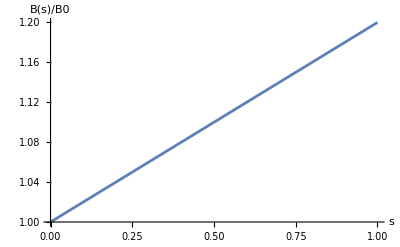

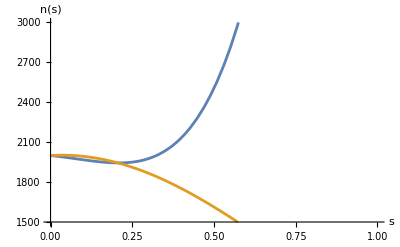

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Tpar0=100;
Tperp0=100;
B0=100;
B[s_]=20*s+B0;

n0=2000;

κ=2.5;

ΔPE[s_]=100*s^2;
κperp=κ;
A0=Tperp0/Tpar0;

G[s_]=(ⅇ^(((B[s]-B0) Tperp0 κ)/(B0 Tpar0)) π (((-1+B[s]/B0) Tperp0 κ)/Tpar0)^κ Csc[π κ])/Gamma[κ];
exprn1[s_]=n0*B[s]/B0*(ⅇ^(-ΔPE[s]/Tpar0))*(Hypergeometric2F1[1,1,1-κperp,κ*A0*(B[s]/B0-1)] - G[s]);
exprn2[s_]=n0*κ*B[s]/B0*Exp[-ΔPE[s]/Tpar0+A0*(B[s]/B0-1)]*ExpIntegralE[1+κ,A0*(B[s]/B0-1)];




Plot[{(B[s]/B0)/A0},{s,0,1},AxesLabel->{"s","B(s)/B0"}]
Plot[{exprn1[s],exprn2[s]},{s,0,1},AxesLabel->{"s","n(s)"},PlotRange->{1500,3000}]
```

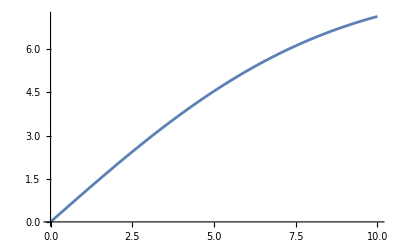

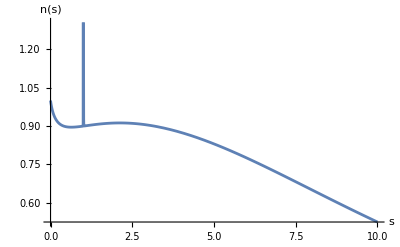

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Tpar0=100;
Tperp0=100;
B0=1;
B[s_]=s+B0;

n0=2000;

κperp=2.5;
κpar=2.5;

ΔPE[s_]=s^2;
λ0=κperp/κpar;
A0=Tperp0/Tpar0;
δ[s_]=(λ0*A0*(B[s]/B0-1))/(ΔPE[s]/(κpar*Tpar0)+1);
G[s_]=(Pi*Csc[Pi*κperp]*Gamma[κpar+κperp+1/2]*δ[s]^κperp*(1-δ[s])^(-κperp-κpar-1/2))/(Gamma[κpar+1/2]*Gamma[κperp]);
exprn[s_]=B[s]/B0*((λ0*A0*(B[s]/B0-1))^(-κpar-1/2))*(δ[s]^(κpar+1/2))*(Hypergeometric2F1[1,1/2+κpar,1-κperp,δ[s]] - G[s]);
Plot[δ[s],{s,0,10}]
Plot[Re[exprn[s]],{s,0,10},AxesLabel->{"s","n(s)"}]
```

```mathematica
exprn[0.67]
```

0.652173-3.60626×10^-11 ⅈ

```mathematica
exprn[0.49]
exprn[0.5]
exprn[0.51]
```

0.680255

11.9283

0.677274+0.000137385 ⅈ

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
C0=(m^(3/2) n0 Gamma[κ])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κ) Gamma[-1/2+κ])
θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];
assumps={κ>3/2,Tpar0>0,Tperp0>0,m>0,A0>0,d>0,ΔPE∈Reals};

FullSimplify[2*Pi*C0*Integrate[vperp*(1+(m/2*vpar^2+ΔPE)/(κ*Tpar0)+ (m*vperp^2(A0+(1-A0)*d))/(2*κ*Tperp0))^(-(κ+1)),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps]]//TraditionalForm
```

(m^(3/2) n0 Gamma[κ])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κ) Gamma[-1/2+κ])

ConditionalExpression[(√(1/m) √m n0 ((κ Tpar0)/(ΔPE+κ Tpar0))^(κ-1/2))/(A0 (-d)+A0+d), ΔPE+κ Tpar0≥0]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
C0=(m^(3/2) n0 Gamma[κ])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κ) Gamma[-1/2+κ])
θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];
assumps={κ>3/2,Tpar0>0,Tperp0>0,m>0,A0>0,d>0,ΔPE∈Reals,vpar∈Reals};

FullSimplify[Integrate[vperp*(1+(m/2*vpar^2+ΔPE)/(κ*Tpar0)+ (m*vperp^2(A0+(1-A0)*d))/(2*κ*Tperp0))^(-(κ+1)),{vperp,0,Infinity},Assumptions->assumps],assumps]
```

(m^(3/2) n0 Gamma[κ])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κ) Gamma[-1/2+κ])

ConditionalExpression[(2^κ Tperp0 (Tpar0 κ)^κ (m vpar^2+2 ΔPE+2 Tpar0 κ)^-κ)/((A0+d-A0 d) m), m vpar^2+2 ΔPE+2 Tpar0 κ>0]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
C0=(m^(3/2) n0 Gamma[κ])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κ) Gamma[-1/2+κ])
θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];
assumps={κ>3/2,Tpar0>0,Tperp0>0,m>0,A0>0,d>0,ΔPE∈Reals};

FullSimplify[2*Pi*C0*Integrate[(2^κ Tperp0 (Tpar0 κ)^κ (m vpar^2+2 ΔPE+2 Tpar0 κ)^-κ)/((A0+d-A0 d) m),{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]//TraditionalForm
```

(m^(3/2) n0 Gamma[κ])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κ) Gamma[-1/2+κ])

ConditionalExpression[(n0 ((κ Tpar0)/(ΔPE+κ Tpar0))^(κ-1/2))/(A0 (-d)+A0+d), ΔPE+κ Tpar0≥0]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κpar>1/2,κperp>1,m>0,Tperp0>0,B>0,B0>0,ΔPE∈Reals,Tpar0>0};
assumps2={κpar>1/2,κperp>1,m>0,Tperp0>0,B>0,B0>0,ΔPE∈Reals,Tpar0>0,n0>=0};
E0=ΔPE+1/2*m*vperp^2*(1-B0/B)
FullSimplify[((m^(3/2) n0 Gamma[1+κpar])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κpar) Gamma[1/2+κpar]))*2*Pi*Integrate[vperp*,{vperp,0,Infinity},Assumptions->assumps],assumps2]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps2={κpar>1/2,κperp>1,m>0,Tperp0>0,ΔPE∈Reals,Tpar0>0,n0>=0,d>0,ΔPE+Tpar0 κpar>0,d<1};
FullSimplify[2*Pi*((m^(3/2) n0 Gamma[1+κpar])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κpar) Gamma[1/2+κpar]))*Integrate[vperp*((√(2 π) Tpar0 ((Tpar0 κpar)/(ΔPE+1/2*m*vperp^2*(1-d)+Tpar0 κpar))^κpar Gamma[1/2+κpar])/(√(m (ΔPE+1/2*m*vperp^2*(1-d)+Tpar0 κpar)) Gamma[κpar]))*((1+(m*d*vperp^2)/(2*κperp*Tperp0))^(-(κperp+1))),{vperp,0,Infinity},Assumptions->assumps2],assumps2]
```

1/d n0 ((Tpar0 κpar)/(ΔPE+Tpar0 κpar))^(1/2+κpar) (-((π (d (ΔPE+Tpar0 κpar))^(1/2+κpar) (-((-1+d) Tperp0 κperp))^κperp (d (ΔPE+Tpar0 κpar)+(-1+d) Tperp0 κperp)^(-1/2-κpar-κperp) Csc[π κperp] Gamma[1/2+κpar+κperp])/(Gamma[1/2+κpar] Gamma[κperp]))+Hypergeometric2F1[1,1/2+κpar,1-κperp,-((-1+d) Tperp0 κperp)/(d (ΔPE+Tpar0 κpar))])

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps2={κpar>1/2,κperp>1,m>0,Tperp0>0,ΔPE∈Reals,Tpar0>0,n0>=0,d>0,vperp>=0};

FullSimplify[(√(2 π) Tpar0 ((Tpar0 κpar)/(ΔPE+1/2*m*vperp^2*(1-d)+Tpar0 κpar))^κpar Gamma[1/2+κpar])/(√(m (ΔPE+1/2*m*vperp^2*(1-d)+Tpar0 κpar)) Gamma[κpar])==(Sqrt[(2*Pi*Tpar0)/(m*κpar)]*Gamma[κpar+1/2]/Gamma[κpar]*(1+(ΔPE+1/2*m*vperp^2*(1-d))/(κpar*Tpar0))^(-κpar-1/2)),assumps2]
```

(-((-1+d) m vperp^2)+2 (ΔPE+Tpar0 κpar))^(-1/2-κpar) (-1+(1/(-((-1+d) m vperp^2)+2 (ΔPE+Tpar0 κpar)))^κpar (-((-1+d) m vperp^2)+2 (ΔPE+Tpar0 κpar))^κpar)==0

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps2={κpar>1/2,κperp>1,m>0,Tperp0>0,ΔPE∈Reals,Tpar0>0,d>0,d<1,vperp>=0,ΔPE+1/2*m*vperp^2*(1-d)+Tpar0 κpar≥0};
E0=ΔPE+1/2*m*vperp^2*(1-d)
FullSimplify[(√(2 π) Tpar0 ((Tpar0 κpar)/(E0+Tpar0 κpar))^κpar Gamma[1/2+κpar])/(√(m (E0+Tpar0 κpar)) Gamma[κpar])==(Sqrt[(2*Pi*Tpar0)/(m*κpar)]*Gamma[κpar+1/2]/Gamma[κpar]*(1+(ΔPE+1/2*m*vperp^2*(1-d))/(κpar*Tpar0))^(-κpar-1/2)),assumps2]
```

1/2 (1-d) m vperp^2+ΔPE

(-((-1+d) m vperp^2)+2 (ΔPE+Tpar0 κpar))^(-1/2-κpar) (-1+(1/(-((-1+d) m vperp^2)+2 (ΔPE+Tpar0 κpar)))^κpar (-((-1+d) m vperp^2)+2 (ΔPE+Tpar0 κpar))^κpar)==0

```mathematica
FullSimplify[(√(2 π) Tpar0 ((Tpar0 κpar)/(ΔPE+1/2*m*vperp^2*(1-d)+Tpar0 κpar))^κpar Gamma[1/2+κpar])/(√(m (ΔPE+1/2*m*vperp^2*(1-d)+Tpar0 κpar)) Gamma[κpar])==(√(2 π) Tpar0 ((Tpar0 κpar)/(E0+Tpar0 κpar))^κpar Gamma[1/2+κpar])/(√(m (E0+Tpar0 κpar)) Gamma[κpar])]
```

True

```mathematica
FullSimplify[(1/x)^k/Sqrt[x]==x^(-k-1/2),{x>0,k>0}]
```

True

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps2={κpar>1/2,κperp>1,m>0,Tperp0>0,ΔPE∈Reals,Tpar0>0,d>0,ΔPE+Tpar0 κpar>0,d<1,A0>0,δ>0,λ0>=0};
Tperp0=A0*Tpar0;
κperp=λ0*κpar;
ΔPE=κpar*Tpar0*((λ0*A0*(1/d-1))/δ-1);


FullSimplify[1/d ((Tpar0 κpar)/(ΔPE+Tpar0 κpar))^(1/2+κpar) (-((π (d (ΔPE+Tpar0 κpar))^(1/2+κpar) (-((-1+d) Tperp0 κperp))^κperp (d (ΔPE+Tpar0 κpar)+(-1+d) Tperp0 κperp)^(-1/2-κpar-κperp) Csc[π κperp] Gamma[1/2+κpar+κperp])/(Gamma[1/2+κpar] Gamma[κperp]))+Hypergeometric2F1[1,1/2+κpar,1-κperp,-((-1+d) Tperp0 κperp)/(d (ΔPE+Tpar0 κpar))]),assumps2]//TraditionalForm
```

-(((1-δ)^(-κpar (λ0+1)-1/2) δ^(κpar λ0) ((d δ)/(A0 λ0-A0 d λ0))^(κpar+1/2) (κpar+1/2 κpar λ0+1 δ-κpar λ0λ0 κpar+κpar+1/2+π csc(π κpar λ0) λ0 κpar+κpar+1/2))/(d κpar+1/2 κpar λ0))

```mathematica
Remove["Global`*"]
ClearAll["context`*"]
assumps2={κpar>1/2,κperp>1,m>0,Tperp0>0,ΔPE∈Reals,Tpar0>0,d>0,ΔPE+Tpar0 κpar>0,d<1,A0>0,δ>0,λ0>0,B>B0,B>0,B0>0};
d=B0/B;
FullSimplify[-(((1-δ)^(-1/2-κpar (1+λ0)) δ^(κpar λ0) ((d δ)/(A0 λ0-A0 d λ0))^(1/2+κpar) (Beta[δ,-κpar λ0,1/2+κpar+κpar λ0] Gamma[1/2+κpar] Gamma[1+κpar λ0]+π Csc[π κpar λ0] Gamma[1/2+κpar+κpar λ0]))/(d Gamma[1/2+κpar] Gamma[κpar λ0])),assumps2]//TraditionalForm
```

-((B (1-δ)^(-κpar (λ0+1)-1/2) δ^(κpar λ0) ((B0 δ)/(A0 B λ0-A0 B0 λ0))^(κpar+1/2) (κpar+1/2 κpar λ0+1 δ-κpar λ0λ0 κpar+κpar+1/2+π csc(π κpar λ0) λ0 κpar+κpar+1/2))/(B0 κpar+1/2 κpar λ0))

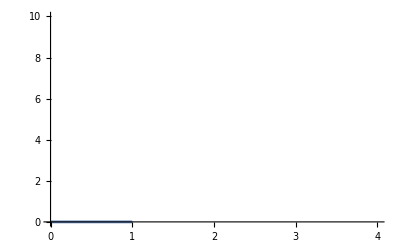

```mathematica
Plot[Im[Beta[x,1/2,1/2]],{x,0,2},PlotRange->{{0,4},{0,10}}]
```

1/(1+5 s)

-((133326. (1+5 s) (s/(1+0.222222 s^2))^2.5 (s/((1+5 s) (1+0.222222 s^2) (0.555556-0.555556/(1+5 s))))^5. (5878.72+79.7604 Beta[(2.77778 s)/(1+0.222222 s^2),-2.5,7.5]))/(1-(2.77778 s)/(1+0.222222 s^2))^7.5)

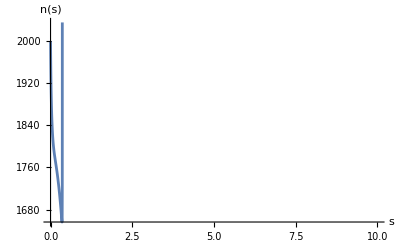

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Tpar0=100;
Tperp0=100;
B0=1;
B[s_]=5*s+B0;
d[s_]=B0/B[s]
n0=2000;

κperp=2.5;
κpar=4.5;

ΔPE[s_]=100*s^2;
λ0=κperp/κpar;
A0=Tperp0/Tpar0;
δ[s_]=(λ0*A0*(B[s]/B0-1))/(ΔPE[s]/(κpar*Tpar0)+1);

exprn[s_]=-n0*(((1-δ[s])^(-1/2-κpar (1+λ0)) δ[s]^(κpar λ0) ((d[s]*δ[s])/(A0 λ0-A0 d[s] λ0))^(1/2+κpar) (Beta[δ[s],-κpar λ0,1/2+κpar+κpar λ0] Gamma[1/2+κpar] Gamma[1+κpar λ0]+π Csc[π κpar λ0] Gamma[1/2+κpar+κpar λ0]))/(d[s] Gamma[1/2+κpar] Gamma[κpar λ0]))

Plot[exprn[s],{s,0,10},AxesLabel->{"s","n(s)"}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps2={κperp>3/2,m>0,Tperp0>0,ΔPE∈Reals,Tpar0>0,d>0,d<1,A0>0};
λ0=κperp/κpar;
(*A0=Tperp0/Tpar0;*)
δ=(κperp/κpar*A0*(1/d-1))/(ΔPE[s]/(κpar*Tpar0)+1);
-(((1-δ)^(-κpar (λ0+1)-1/2) δ^(κpar λ0) ((d δ)/(A0 λ0-A0 d λ0))^(κpar+1/2) (Gamma[κpar+1/2] Gamma[κpar λ0+1] Beta[δ,-κpar λ0,λ0 κpar+κpar+1/2]+π csc(π κpar λ0) Gamma[λ0 κpar+κpar+1/2]))/(d Gamma[κpar+1/2] Gamma[κpar λ0]))
Limit[-(((Beta[(A0 (-1+B/B0) κperp)/(κpar (1+ΔPE[s]/(Tpar0 κpar))),-κperp,1/2+κpar+κperp] Gamma[1/2+κpar] Gamma[1+κperp]+csc π^2 κperp Gamma[1/2+κpar+κperp]) ((A0 (-1+B/B0) κperp)/(κpar (1+ΔPE[s]/(Tpar0 κpar))))^κperp ((A0 (-1+B/B0) d κperp)/(κpar ((A0 κperp)/κpar-(A0 d κperp)/κpar) (1+ΔPE[s]/(Tpar0 κpar))))^(1/2+κpar) (1-(A0 (-1+B/B0) κperp)/(κpar (1+ΔPE[s]/(Tpar0 κpar))))^(-1/2-κpar (1+κperp/κpar)))/(d Gamma[1/2+κpar] Gamma[κperp])),κpar->Infinity,Assumptions->assumps2]//TraditionalForm
```

Limit[-((((A0 κperp (B/B0-1))/(κpar ((ΔPE(s))/(κpar Tpar0)+1)))^κperp (1-(A0 κperp (B/B0-1))/(κpar ((ΔPE(s))/(κpar Tpar0)+1)))^(-κpar (κperp/κpar+1)-1/2) ((A0 d κperp (B/B0-1))/(κpar ((A0 κperp)/κpar-(A0 d κperp)/κpar) ((ΔPE(s))/(κpar Tpar0)+1)))^(κpar+1/2) (κpar+1/2 κperp+1 (A0 (B/B0-1) κperp)/(κpar ((ΔPE(s))/(Tpar0 κpar)+1))-κperpκpar+κperp+1/2+π^2 κperp csc κpar+κperp+1/2))/(d κpar+1/2 κperp)),κpar→∞,Assumptions→{κperp>3/2,m>0,Tperp0>0,ΔPE∈ℝ,Tpar0>0,d>0,d<1,A0>0}]

```mathematica
exprn2[s_]=n0*κ*B[s]/B0*Exp[-ΔPE[s]/Tpar0+A0*(B[s]/B0-1)]*ExpIntegralE[1+κ,A0*(B[s]/B0-1)];
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps2={κperp>3/2,m>0,Tperp0>0,ΔPE∈Reals,Tpar0>0,d>0,d<1,A0>0};

FullSimplify[ExpIntegralE[n,x]==x^(n-1)*Gamma[1-n,x]]

FullSimplify[ExpIntegralE[1+κ,A0*(B/B0-1)] == (A0*(B/B0-1))^κ*Gamma[-κ,A0*(B/B0-1)]]
```

True

True

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps2={κ>3/2,m>0,Tperp0>0,ΔPE∈Reals,Tpar0>0,d>0,d<1,A0>0};

FullSimplify[κ*1/d*Exp[-ΔPE/Tpar0+A0*(1/d-1)]*(A0*(1/d-1))^κ*Gamma[-κ,A0*(1/d-1)],assumps2]
```

(ⅇ^(A0 (-1+1/d)-ΔPE/Tpar0) κ ExpIntegralE[1+κ,A0 (-1+1/d)])/d

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={B>0,B0>0,A0>0};
FullSimplify[Integrate[(1-A0/(A0+(1-A0)*B0/B))*1/B,B,Assumptions->assumps],assumps]
```

Log[B]-Log[A0 B+B0-A0 B0]

```mathematica
Simplify[A0 B+B0-A0 B0 == B*(A0+(1-A0)*B0/B)]
```

True

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κ>=3/2,A0>0,d>0,d<=1};
assumps2={κ>=3/2,A0>0,d>0,ΔPE∈Reals,Tpar0>0,Tperp0>0,m>0,d<=1};
C0=n0/(Tperp0*Sqrt[Tpar0])*(m/(2*Pi))^(3/2);

FullSimplify[2*Pi*C0*Exp[-ΔPE/Tpar0]*Sqrt[Pi*(2*Tpar0)/m]*(2*κ*Tperp0/m)*Integrate[u*((1+d*u^2)^(-(1+κ)))*Exp[-A0*κ*u^2*(1-d)],{u,0,Infinity},Assumptions->assumps],assumps2]
```

(ⅇ^(-ΔPE/Tpar0+A0 (-1+1/d) κ) n0 κ ExpIntegralE[1+κ,A0 (-1+1/d) κ])/d

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κ>=3/2,A0>0,d>0};

Integrate[u*((1+d*u^2)^(-(1+κ)))*Exp[-A0*κ*u^2*(1-d)],{u,0,Infinity},Assumptions->assumps]
```

ConditionalExpression[(ⅇ^(A0 (-1+1/d) κ) ExpIntegralE[1+κ,A0 (-1+1/d) κ])/(2 d), d≤1]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={m>0,Tpar0>0};

Integrate[Exp[-m*vpar^2/(2*Tpar0)],{vpar,-Infinity,Infinity},Assumptions->assumps]
```

√(2 π) √(Tpar0/m)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={x>0};
(*x = A0 (-1+1/d)*)
Limit[ⅇ^(x*κ) *κ*ExpIntegralE[1+κ,x*κ],κ->Infinity,Assumptions->{x>=0}]
```

Limit[ⅇ^(x κ) κ ExpIntegralE[1+κ,x κ],κ→∞,Assumptions→{x>0}]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={B>0,B0>0,B>=B0,A0>0};
(*x = A0 (-1+1/d)*)
FullSimplify[(B/B0)/(1+A0 (-1+B/B0))==(1/(A0+(1-A0)*B0/B))]
```

True

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*x = A0 (-1+1/d)*)
Integrate[Exp[-(1+x)*u],{u,0,Infinity},Assumptions->{x>=0}]
```

1/(1+x)

```mathematica
Limit[Exp[
u/κ],κ->Infinity,Assumptions->u>=0]
```

1

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Limit[ExpIntegralE[1+κ,x*κ],κ->Infinity,Assumptions->{x>=0}]
```

Limit[ExpIntegralE[1+κ,x κ],κ→∞,Assumptions→{x≥0}]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Limit[(x*κ)^κ*Gamma[-κ,x*κ],κ->Infinity,Assumptions->{x>=0}]
```

Limit[(x κ)^κ Gamma[-κ,x κ],κ→∞,Assumptions→{x≥0}]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
FullSimplify[(x*κ)^κ*Gamma[-κ,x*κ]==ExpIntegralE[1+κ,x*κ],{x>=0,κ>3/2}]
```

True

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Limit[ⅇ^(x*κ) *κ*(x*κ)^κ*Gamma[-κ,x*κ],κ->Infinity,Assumptions->{x>=0}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κ>3/2,θ>0};

FullSimplify[Solve[n==A*Integrate[4*Pi*v^2*(1+v^2/(κ*θ^2))^(-(κ+1)),{v,0,Infinity},Assumptions->assumps],A,Assumptions->assumps],assumps]
```

Remove::rmnsm: There are no symbols matching "Global`*".

{{A→(n Gamma[κ])/(π^(3/2) θ^3 √κ Gamma[-1/2+κ])}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={κ>3/2,θpar>0,θperp>0,m>0};

FullSimplify[Solve[n==A*2*Pi*Integrate[vperp*(1+vpar^2/(κ*θpar^2)+ vperp^2/(κ*θperp^2))^(-(κ+1)),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],A,Assumptions->assumps],assumps]
```

{{A→(n Gamma[κ])/(π^(3/2) θpar θperp^2 √κ Gamma[-1/2+κ])}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κ>3/2,Tc>0,m>0,n>0};
θ=Sqrt[2*Tc/m];
c=(n Gamma[κ])/(π^(3/2) θ^3 √κ Gamma[-1/2+κ]);
FullSimplify[(c*Integrate[m*v^2*(4*Pi*v^2*(1+v^2/(κ*θ^2))^(-(κ+1))),{v,0,Infinity},Assumptions->assumps])/(3*n),assumps]
```

(2 Tc κ)/(-3+2 κ)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={θpar>0,θperp>0,m>0};

FullSimplify[Solve[n==A*2*Pi*Integrate[vperp*Exp[-vpar^2/θpar^2- vperp^2/θperp^2],{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],A,Assumptions->assumps],assumps]
```

{{A→n/(π^(3/2) θpar θperp^2)}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={Tpar>0,Tperp>0,n>0,m>0};
θpar=Sqrt[2*Tpar/m];
θperp=Sqrt[2*Tperp/m];
c=n/(π^(3/2) θpar θperp^2);
FullSimplify[1/3*(c*2*Pi*Integrate[m*vperp*vperp(vperp*Exp[-(m*vpar^2)/(2*Tpar)- (m*vperp^2)/(2*Tperp)]),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps]+c*2*Pi*Integrate[m*vpar*vpar(vperp*Exp[-(m*vpar^2)/(2*Tpar)- (m*vperp^2)/(2*Tperp)]),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps]),assumps]
```

1/3 n (Tpar+2 Tperp)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={T>0,m>0};

FullSimplify[Solve[n==c*4*Pi*Integrate[v^2*Exp[-(m*v^2)/(2*T)],{v,0,Infinity},Assumptions->assumps],c,Assumptions->assumps],assumps]
```

{{c→(n (m/T)^(3/2))/(2 √2 π^(3/2))}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={T>0,m>0,n>0};
c=(n (m/T)^(3/2))/(2 √2 π^(3/2));
FullSimplify[c*4*Pi*Integrate[m*v^2*(v^2*Exp[-(m*v^2)/(2*T)]),{v,0,Infinity},Assumptions->assumps],assumps]
```

3 n T

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={Tparc>0,Tperpc>0,n>0,m>0};
θpar=Sqrt[2*Tpar/m];
θperp=Sqrt[2*Tperp/m];
c=n/(π^(3/2) θpar θperp^2);
FullSimplify[1/3*(c*2*Pi*Integrate[m*vperp*vperp(vperp*Exp[-(m*vpar^2)/(2*Tpar)- (m*vperp^2)/(2*Tperp)]),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps]+c*2*Pi*Integrate[m*vpar*vpar(vperp*Exp[-(m*vpar^2)/(2*Tpar)- (m*vperp^2)/(2*Tperp)]),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps]),assumps]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={Tpar>0,Tperp>0,n>0,m>0};
θpar=Sqrt[2*Tpar/m];
θperp=Sqrt[2*Tperp/m];
c=n/(π^(3/2) θpar θperp^2);
FullSimplify[c*2*Pi*Integrate[m*vperp*vperp(vperp*Exp[-(m*vpar^2)/(2*Tpar)- (m*vperp^2)/(2*Tperp)]),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps]/(2*n),assumps]

FullSimplify[c*2*Pi*Integrate[m*vpar*vpar(vperp*Exp[-(m*vpar^2)/(2*Tpar)- (m*vperp^2)/(2*Tperp)]),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps]/(n),assumps]
```

Tperp

Tpar

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={Tparc>0,Tperpc>0,n>0,m>0,κ>3/2};
θpar=Sqrt[2*Tparc/m];
θperp=Sqrt[2*Tperpc/m];
c=(n Gamma[κ])/(π^(3/2) θpar θperp^2 √κ Gamma[-1/2+κ]);
FullSimplify[c*2*Pi*Integrate[m*vperp*vperp(vperp*(1+vpar^2/(κ*θpar^2)+ vperp^2/(κ*θperp^2))^(-(κ+1))),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps]/(2*n),assumps]

FullSimplify[c*2*Pi*Integrate[m*vpar*vpar(vperp*(1+vpar^2/(κ*θpar^2)+ vperp^2/(κ*θperp^2))^(-(κ+1))),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps]/(n),assumps]
```

(2 Tperpc κ)/(-3+2 κ)

(2 Tparc κ)/(-3+2 κ)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={Tparc>0,Tperpc>0,m>0,κ>1};

FullSimplify[Solve[n==c*2*Pi*Integrate[vperp*Exp[-(m*vpar^2)/(2*Tparc)]*(1+(m*vperp^2)/(2*κ*Tperpc))^(-(1+κ)),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],c,Assumptions->assumps],assumps]
```

{{c→(m^(3/2) n)/(2 √2 π^(3/2) √Tparc Tperpc)}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={Tparc>0,Tperpc>0,n>0,m>0,κ>3/2};
θpar=Sqrt[2*Tparc/m];
θperp=Sqrt[2*Tperpc/m];
c=(m^(3/2) n)/(2 √2 π^(3/2) √Tparc Tperpc);
FullSimplify[c*2*Pi*Integrate[m*vperp*vperp(vperp*Exp[-vpar^2/θpar^2]*(1+ vperp^2/(κ*θperp^2))^(-(κ+1))),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps]/(2*n),assumps]

FullSimplify[c*2*Pi*Integrate[m*vpar*vpar(vperp*Exp[-vpar^2/θpar^2]*(1+ vperp^2/(κ*θperp^2))^(-(κ+1))),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps]/(n),assumps]
```

(Tperpc κ)/(-1+κ)

Tparc

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
C0=(m^(3/2) n0)/(2 √2 π^(3/2) √Tpar0 Tperp0)
assumps={Tpar0>0,Tperp0>0,m>0,A0>0,d>0,ΔPE∈Reals,vpar∈Reals};

FullSimplify[2*Pi*C0*Integrate[m*vperp^3*Exp[-(m/2*vpar^2+ΔPE)/Tpar0 -(m*vperp^2(A0+(1-A0)*d))/(2*Tperp0)],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]/(2*n0),assumps]

FullSimplify[2*Pi*C0*Integrate[m*vperp*vpar^2*Exp[-(m/2*vpar^2+ΔPE)/Tpar0 -(m*vperp^2(A0+(1-A0)*d))/(2*Tperp0)],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]/(n0),assumps]
```

(m^(3/2) n0)/(2 √2 π^(3/2) √Tpar0 Tperp0)

ConditionalExpression[(ⅇ^(-ΔPE/Tpar0) Tperp0)/(A0+d-A0 d)^2, A0 d<A0+d]

ConditionalExpression[(ⅇ^(-ΔPE/Tpar0) Tpar0)/(A0+d-A0 d), A0 d<A0+d]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
C0=(m^(3/2) n0 Gamma[κ])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κ) Gamma[-1/2+κ])
θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];
assumps={κ>3/2,Tpar0>0,Tperp0>0,m>0,A0>0,d>0,ΔPE∈Reals,vpar∈Reals};

FullSimplify[Integrate[vperp*(1+(m/2*vpar^2+ΔPE)/(κ*Tpar0)+ (m*vperp^2(A0+(1-A0)*d))/(2*κ*Tperp0))^(-(κ+1)),{vperp,0,Infinity},Assumptions->assumps],assumps]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
C0=(m^(3/2) n0)/(2 √2 π^(3/2) √Tpar0 Tperp0);
assumps={Tpar0>0,Tperp0>0,m>0,A0>0,d>0,ΔPE∈Reals};
n=FullSimplify[2*Pi*C0*Integrate[vperp*Exp[-(m/2*vpar^2+ΔPE)/Tpar0 -(m*vperp^2(A0+(1-A0)*d))/(2*Tperp0)],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps];
FullSimplify[2*Pi*C0*Integrate[m*vperp^3*Exp[-(m/2*vpar^2+ΔPE)/Tpar0 -(m*vperp^2(A0+(1-A0)*d))/(2*Tperp0)],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]/(2*n),assumps]

FullSimplify[2*Pi*C0*Integrate[m*vperp*vpar^2*Exp[-(m/2*vpar^2+ΔPE)/Tpar0 -(m*vperp^2(A0+(1-A0)*d))/(2*Tperp0)],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]/(n),assumps]
```

ConditionalExpression[Tperp0/(A0+d-A0 d), A0 d<A0+d]

ConditionalExpression[Tpar0, A0 d<A0+d]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
C0=(m^(3/2) n0 Gamma[κ])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κ) Gamma[-1/2+κ]);
assumps={κ>3/2,Tpar0>0,Tperp0>0,m>0,A0>0,d>0,ΔPE∈Reals,ΔPE/(κ*Tpar0)>-1,A0 d<A0+d};(*,d<1*)
n=FullSimplify[2*Pi*C0*Integrate[vperp*(1+(m/2*vpar^2+ΔPE)/(κ*Tpar0) +(m*vperp^2(A0+(1-A0)*d))/(2*κ*Tperp0))^(-(1+κ)),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[2*Pi*C0*Integrate[m*vperp^3*(1+(m/2*vpar^2+ΔPE)/(κ*Tpar0) +(m*vperp^2(A0+(1-A0)*d))/(2*κ*Tperp0))^(-(1+κ)),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]/(2*n),assumps]

FullSimplify[2*Pi*C0*Integrate[m*vperp*vpar^2*(1+(m/2*vpar^2+ΔPE)/(κ*Tpar0) +(m*vperp^2(A0+(1-A0)*d))/(2*κ*Tperp0))^(-(1+κ)),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]/(n),assumps]
```

(n0 ((Tpar0 κ)/(ΔPE+Tpar0 κ))^(-1/2+κ))/(A0+d-A0 d)

(2 Tperp0 (ΔPE+Tpar0 κ))/((A0+d-A0 d) Tpar0 (-3+2 κ))

(2 (ΔPE+Tpar0 κ))/(-3+2 κ)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
C0=(m^(3/2) n0 Gamma[κ])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κ) Gamma[-1/2+κ]);
assumps={κ>3/2,Tpar0>0,Tperp0>0,m>0,A0>0,d>0,ΔPE∈Reals,ΔPE/(κ*Tpar0)>-1,A0 d<A0+d};(*,d<1*)

FullSimplify[2*Pi*C0*Integrate[m*vperp^3*(1+(m/2*vpar^2)/(κ*Tpar0) +(m*vperp^2)/(2*κ*Tperp0))^(-(1+κ)),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]/(2*n0),assumps]

FullSimplify[2*Pi*C0*Integrate[m*vperp*vpar^2*(1+(m/2*vpar^2)/(κ*Tpar0) +(m*vperp^2)/(2*κ*Tperp0))^(-(1+κ)),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]/(n0),assumps]
```

(2 Tperp0 κ)/(-3+2 κ)

(2 Tpar0 κ)/(-3+2 κ)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κ>3/2,κ0>3/2,Tpar0>0,Tperp0>0,Tpar>0,Tperp>0,m>0,A0>0,d>0,ΔPE∈Reals,ΔPE/(κ*Tpar0)>-1,A0 d<A0+d};
FullSimplify[Solve[(2 Tperp κ)/(-3+2 κ)==(2 Tperp0 (ΔPE+Tpar0 κ0))/((A0+d-A0 d) Tpar0 (-3+2 κ0)),Tperp,Assumptions->assumps],assumps]
FullSimplify[Solve[(2 Tpar κ)/(-3+2 κ)==(2 (ΔPE+Tpar0 κ0))/(-3+2 κ0),Tpar,Assumptions->assumps],assumps]
```

{{Tperp→ConditionalExpression[(Tperp0 (-3+2 κ) (ΔPE+Tpar0 κ0))/((A0+d-A0 d) Tpar0 κ (-3+2 κ0)), (κ<κ0||(ΔPE+Tpar0 κ0>0&&κ>κ0))&&d≠1]}}

{{Tpar→ConditionalExpression[((-3+2 κ) (ΔPE+Tpar0 κ0))/(κ (-3+2 κ0)), (ΔPE+Tpar0 κ0>0&&κ>κ0)||κ<κ0]}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κ>3/2,κ0>3/2,Tpar0>0,Tperp0>0,m>0,A0>0,d>0,ΔPE∈Reals,ΔPE/(κ*Tpar0)>-1,A0 d<A0+d,Tpar>0,Tperp>0};

FullSimplify[Solve[(2 Tpar0 κ)/(-3+2 κ)==(2 (ΔPE+Tpar0 κ0))/(-3+2 κ0),κ,Assumptions->assumps],assumps]
```

{{κ→ConditionalExpression[(3 (ΔPE+Tpar0 κ0))/(3 Tpar0+2 ΔPE), ΔPE>0||(ΔPE<0&&Tpar0>-(2 ΔPE)/3)]}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κ>3/2,κ0>3/2,Tpar0>0,Tperp0>0,Tpar>0,Tperp>0,m>0,A0>0,d>0,ΔPE∈Reals,ΔPE/(κ*Tpar0)>-1,A0 d<A0+d};
FullSimplify[Solve[(2 Tperp (3 (ΔPE+Tpar0 κ0))/(3 Tpar0+2 ΔPE))/(-3+2 (3 (ΔPE+Tpar0 κ0))/(3 Tpar0+2 ΔPE))==(2 Tperp0 (ΔPE+Tpar0 κ0))/((A0+d-A0 d) Tpar0 (-3+2 κ0)),Tperp,Assumptions->assumps],assumps]
```

{{Tperp→ConditionalExpression[Tperp0/(A0+d-A0 d), d≠1]}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={Tpar>0,Tperp>0,n>0,m>0};
θpar=Sqrt[2*Tpar/m];
θperp=Sqrt[2*Tperp/m];
c=n/(π^(3/2) θpar θperp^2);
FullSimplify[c*2*Pi*Integrate[vperp*(vperp*Exp[-(m*vpar^2)/(2*Tpar)- (m*vperp^2)/(2*Tperp)]),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps]/(2*n),assumps]

FullSimplify[c*2*Pi*Integrate[vpar*(vperp*Exp[-(m*vpar^2)/(2*Tpar)- (m*vperp^2)/(2*Tperp)]),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps]/(n),assumps]
```

1/2 √(π/2) √(Tperp/m)

0

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
C0=(m^(3/2) n0 Gamma[κ])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κ) Gamma[-1/2+κ]);
assumps={κ>3/2,Tpar0>0,Tperp0>0,m>0,A0>0,d>0,ΔPE∈Reals,ΔPE/(κ*Tpar0)>-1,A0 d<A0+d};(*,d<1*)

FullSimplify[2*Pi*C0*Integrate[vperp^2*(1+(m/2*vpar^2)/(κ*Tpar0) +(m*vperp^2)/(2*κ*Tperp0))^(-(1+κ)),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]/(2*n0),assumps]

FullSimplify[2*Pi*C0*Integrate[vperp*vpar*(1+(m/2*vpar^2)/(κ*Tpar0) +(m*vperp^2)/(2*κ*Tperp0))^(-(1+κ)),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]/(n0),assumps]
```

(√(π/2) √((Tperp0 κ)/m) Gamma[-1+κ])/(2 Gamma[-1/2+κ])

0

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
C0=(m^(3/2) n0 Gamma[κ0])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κ0) Gamma[-1/2+κ0]);
assumps={κ0>3/2,Tpar0>0,Tperp0>0,m>0,A0>0,d>0,ΔPE∈Reals,ΔPE/(κ0*Tpar0)>-1,A0 d<A0+d};(*,d<1*)
n=FullSimplify[2*Pi*C0*Integrate[vperp*(1+(m/2*vpar^2+ΔPE)/(κ0*Tpar0) +(m*vperp^2(A0+(1-A0)*d))/(2*κ0*Tperp0))^(-(1+κ0)),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[2*Pi*C0*Integrate[vperp^2*(1+(m/2*vpar^2+ΔPE)/(κ0*Tpar0) +(m*vperp^2(A0+(1-A0)*d))/(2*κ0*Tperp0))^(-(1+κ0)),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]/(2*n),assumps]
```

(n0 ((Tpar0 κ0)/(ΔPE+Tpar0 κ0))^(-1/2+κ0))/(A0+d-A0 d)

(√(π/2) √((Tperp0 (ΔPE+Tpar0 κ0))/((A0+d-A0 d) m Tpar0)) Gamma[-1+κ0])/(2 Gamma[-1/2+κ0])

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κ>3/2,κ0>3/2,Tpar0>0,Tperp0>0,Tpar>0,Tperp>0,m>0,A0>0,d>0,ΔPE∈Reals,ΔPE/(κ0*Tpar0)>-1,A0 d<A0+d};
FullSimplify[Solve[{(2 Tperp κ)/(-3+2 κ)==(2 Tperp0 (ΔPE+Tpar0 κ0))/((A0+d-A0 d) Tpar0 (-3+2 κ0)),(2 Tpar κ)/(-3+2 κ)==(2 (ΔPE+Tpar0 κ0))/(-3+2 κ0),(√(π/2) √((Tperp κ)/m) Gamma[-1+κ])/(2 Gamma[-1/2+κ])==(√(π/2) √((Tperp0 (ΔPE+Tpar0 κ0))/((A0+d-A0 d) m Tpar0)) Gamma[-1+κ0])/(2 Gamma[-1/2+κ0])},{Tperp,Tpar,κ},Assumptions->assumps],assumps]
```

$Aborted

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
C0=(m^(3/2) n0 Gamma[κ0])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κ0) Gamma[-1/2+κ0]);
assumps={κ0>3/2,Tpar0>0,Tperp0>0,m>0,A0>0,d>0,ΔPE∈Reals,ΔPE/(κ0*Tpar0)>-1,A0 d<A0+d};(*,d<1*)

FullSimplify[2*Pi*C0*Integrate[vperp*vpar^4*(1+(m/2*vpar^2)/(κ0*Tpar0) +(m*vperp^2)/(2*κ0*Tperp0))^(-(1+κ0)),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]/(n0),assumps]
FullSimplify[2*Pi*C0*Integrate[vperp*vperp^4*(1+(m/2*vpar^2)/(κ0*Tpar0) +(m*vperp^2)/(2*κ0*Tperp0))^(-(1+κ0)),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]/(2*n0),assumps]
```

ConditionalExpression[(12 Tpar0^2 κ0^2)/(m^2 (15-16 κ0+4 κ0^2)), κ0>5/2]

ConditionalExpression[(16 Tperp0^2 κ0^2)/(m^2 (15-16 κ0+4 κ0^2)), κ0>5/2]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
C0=(m^(3/2) n0 Gamma[κ0])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κ0) Gamma[-1/2+κ0]);
assumps={κ0>3/2,Tpar0>0,Tperp0>0,m>0,A0>0,d>0,ΔPE∈Reals,ΔPE/(κ0*Tpar0)>-1,A0 d<A0+d};(*,d<1*)
n=(n0 ((Tpar0 κ0)/(ΔPE+Tpar0 κ0))^(-1/2+κ0))/(A0+d-A0 d)
FullSimplify[2*Pi*C0*Integrate[vperp*vpar^4*(1+(m/2*vpar^2+ΔPE)/(κ0*Tpar0) +(m*vperp^2(A0+(1-A0)*d))/(2*κ0*Tperp0))^(-(1+κ0)),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]/(2*n),assumps]
FullSimplify[2*Pi*C0*Integrate[vperp^5*(1+(m/2*vpar^2+ΔPE)/(κ0*Tpar0) +(m*vperp^2(A0+(1-A0)*d))/(2*κ0*Tperp0))^(-(1+κ0)),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]/(2*n),assumps]
```

(n0 ((Tpar0 κ0)/(ΔPE+Tpar0 κ0))^(-1/2+κ0))/(A0+d-A0 d)

ConditionalExpression[(6 (ΔPE+Tpar0 κ0)^2)/(m^2 (-5+2 κ0) (-3+2 κ0)), κ0>5/2]

ConditionalExpression[(16 Tperp0^2 (ΔPE+Tpar0 κ0)^2)/((A0+d-A0 d)^2 m^2 Tpar0^2 (-5+2 κ0) (-3+2 κ0)), κ0>5/2]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κ>5/2,κ0>5/2,Tpar0>0,Tperp0>0,Tpar>0,Tperp>0,m>0,A0>0,d>0,ΔPE∈Reals,ΔPE/(κ0*Tpar0)>-1,A0 d<A0+d};
FullSimplify[Solve[{(2 Tperp κ)/(-3+2 κ)==(2 Tperp0 (ΔPE+Tpar0 κ0))/((A0+d-A0 d) Tpar0 (-3+2 κ0)),(2 Tpar κ)/(-3+2 κ)==(2 (ΔPE+Tpar0 κ0))/(-3+2 κ0),(12 Tpar^2 κ^2)/(m^2 (15-16 κ+4 κ^2))==(12 (ΔPE+Tpar0 κ0)^2)/(m^2 (-5+2 κ0) (-3+2 κ0))},{Tperp,Tpar,κ},Assumptions->assumps],assumps]
```

{{Tperp→ConditionalExpression[(Tperp0 (ΔPE+Tpar0 κ0))/((A0+d-A0 d) Tpar0 κ0), d≠1],Tpar→ConditionalExpression[Tpar0+ΔPE/κ0, d≠1],κ→ConditionalExpression[κ0, d≠1]}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
κ=κ0;
assumps={κ>3/2,κ0>3/2,Tpar0>0,Tperp0>0,Tpar>0,Tperp>0,m>0,A0>0,d>0,ΔPE∈Reals,ΔPE/(κ0*Tpar0)>-1,A0 d<A0+d};
FullSimplify[Solve[{(2 Tperp κ)/(-3+2 κ)==(2 Tperp0 (ΔPE+Tpar0 κ0))/((A0+d-A0 d) Tpar0 (-3+2 κ0)),(2 Tpar κ)/(-3+2 κ)==(2 (ΔPE+Tpar0 κ0))/(-3+2 κ0),(16 Tperp^2 κ^2)/(m^2 (15-16 κ+4 κ^2))==(16 Tperp0^2 (ΔPE+Tpar0 κ0)^2)/((A0+d-A0 d)^2 m^2 Tpar0^2 (-5+2 κ0) (-3+2 κ0))},{Tperp,Tpar},Assumptions->assumps],assumps]
```

{{Tperp→ConditionalExpression[(Tperp0 (ΔPE+Tpar0 κ0))/((A0+d-A0 d) Tpar0 κ0), d≠1],Tpar→ConditionalExpression[Tpar0+ΔPE/κ0, d≠1]}}

True

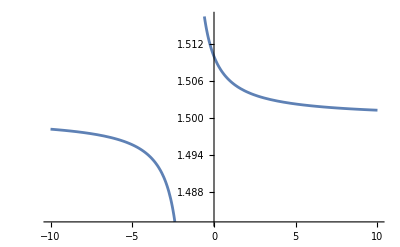

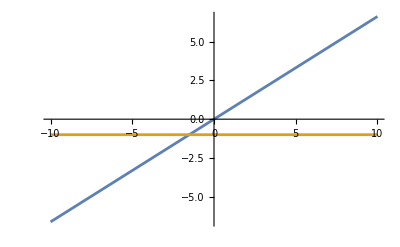

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
κ=κ0;
assumps={κ>3/2,κ0>3/2,Tpar0>0,Tperp0>0,Tpar>0,Tperp>0,m>0,A0>0,d>0,ΔPE∈Reals,ΔPE/(κ0*Tpar0)>-1,A0 d<A0+d};
FullSimplify[(3 (ΔPE+Tpar0 κ0))/(3 Tpar0+2 ΔPE)==(ΔPE/(Tpar0 κ0)+1)/(1/κ0+(2*ΔPE)/(3*Tpar0 κ0)),assumps]
κ0=1.51;
Tpar0=1;
Plot[(ΔPE/(Tpar0 κ0)+1)/(1/κ0+(2*ΔPE)/(3*Tpar0 κ0)),{ΔPE,-10,10}]
Plot[{ΔPE/(Tpar0 κ0),-1},{ΔPE,-10,10}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κ>3/2,κ0>3/2,Tpar0>0,Tperp0>0,Tpar>0,Tperp>0,m>0,A0>0,d>0,ΔPE∈Reals,ΔPE/(κ0*Tpar0)>-1,A0 d<A0+d};
FullSimplify[(12 Tpar0^2 ((3 (ΔPE+Tpar0 κ0))/(3 Tpar0+2 ΔPE))^2)/(m^2 (15-16 (3 (ΔPE+Tpar0 κ0))/(3 Tpar0+2 ΔPE)+4 ((3 (ΔPE+Tpar0 κ0))/(3 Tpar0+2 ΔPE))^2))==(12 (ΔPE+Tpar0 κ0)^2)/(m^2 (-5+2 κ0) (-3+2 κ0)),assumps]
```

ΔPE/((4 ΔPE+Tpar0 (15-6 κ0)) (-5+2 κ0))==0

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={Tpar0>0,Tperp0>0,n0>0,m>0,κ0>2/2,d>0,ΔPE∈Reals,A0>0};
θpar=Sqrt[2*Tpar0/m];
θperp=Sqrt[2*Tperp0/m];
c=(m^(3/2) n0)/(2 √2 π^(3/2) √Tpar0 Tperp0);
n=1/d ⅇ^(-ΔPE/Tpar0+A0 (-1+1/d) κ0) n0 κ0 ExpIntegralE[1+κ0,A0 (-1+1/d) κ0];
FullSimplify[c*2*Pi*Exp[-ΔPE/Tpar0]*m*(2*κ0*Tperp0/m)^2*Integrate[u^3*((1+d*u^2)^(-(1+κ0)))*Exp[-A0*κ0*u^2*(1-d)],{u,0,Infinity},Assumptions->assumps]*Integrate[Exp[-(m*vpar^2/2)/Tpar0],{vpar,-Infinity,Infinity},Assumptions->assumps]/(2*n),assumps]

FullSimplify[c*2*Pi*Exp[-ΔPE/Tpar0]*m*(2*κ0*Tperp0/m)*Integrate[u*((1+d*u^2)^(-(1+κ0)))*Exp[-A0*κ0*u^2*(1-d)],{u,0,Infinity},Assumptions->assumps]*Integrate[vpar^2*Exp[-(m*vpar^2/2)/Tpar0],{vpar,-Infinity,Infinity},Assumptions->assumps]/(n),assumps]
```

ConditionalExpression[(-d ⅇ^((A0 (-1+d) κ0)/d) Tperp0+(A0+d-A0 d) Tperp0 κ0 ExpIntegralE[κ0,A0 (-1+1/d) κ0])/(d^2 ExpIntegralE[1+κ0,A0 (-1+1/d) κ0]), d≤1]

ConditionalExpression[Tpar0, d≤1]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={Tpar0>0,Tperp0>0,n0>0,m>0,κ0>2/2,d>0,d<=1,ΔPE∈Reals,A0>0};
θpar=Sqrt[2*Tpar0/m];
θperp=Sqrt[2*Tperp0/m];
c=(m^(3/2) n0)/(2 √2 π^(3/2) √Tpar0 Tperp0);
n=1/d ⅇ^(-ΔPE/Tpar0+A0 (-1+1/d) κ0) n0 κ0 ExpIntegralE[1+κ0,A0 (-1+1/d) κ0];
FullSimplify[c*2*Pi*Exp[-ΔPE/Tpar0]*(2*κ0*Tperp0/m)^3*Integrate[u^5*((1+d*u^2)^(-(1+κ0)))*Exp[-A0*κ0*u^2*(1-d)],{u,0,Infinity},Assumptions->assumps]*Integrate[Exp[-(m*vpar^2/2)/Tpar0],{vpar,-Infinity,Infinity},Assumptions->assumps]/(2*n),assumps]

FullSimplify[c*2*Pi*Exp[-ΔPE/Tpar0]*(2*κ0*Tperp0/m)*Integrate[u*((1+d*u^2)^(-(1+κ0)))*Exp[-A0*κ0*u^2*(1-d)],{u,0,Infinity},Assumptions->assumps]*Integrate[vpar^4*Exp[-(m*vpar^2/2)/Tpar0],{vpar,-Infinity,Infinity},Assumptions->assumps]/(n),assumps]
```

(2 Tperp0^2 κ0 (d ⅇ^((A0 (-1+d) κ0)/d) (-A0 κ0+d (-1+(-1+A0) κ0))+κ0 (-d^2+(A0+d-A0 d)^2 κ0) ExpIntegralE[-1+κ0,A0 (-1+1/d) κ0]))/(d^4 m^2 (-1+κ0) ExpIntegralE[1+κ0,A0 (-1+1/d) κ0])

(3 Tpar0^2)/m^2

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={Tparc>0,Tperpc>0,n>0,m>0,κ>3/2};
θpar=Sqrt[2*Tparc/m];
θperp=Sqrt[2*Tperpc/m];
c=(m^(3/2) n)/(2 √2 π^(3/2) √Tparc Tperpc);
FullSimplify[c*2*Pi*Integrate[m*vperp^4(vperp*Exp[-vpar^2/θpar^2]*(1+ vperp^2/(κ*θperp^2))^(-(κ+1))),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps]/(2*n),assumps]

FullSimplify[c*2*Pi*Integrate[m*vpar^4(vperp*Exp[-vpar^2/θpar^2]*(1+ vperp^2/(κ*θperp^2))^(-(κ+1))),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps]/(n),assumps]
```

(4 Tperpc^2 κ^2)/(m (2-3 κ+κ^2))

(3 Tparc^2)/m

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
Tpar=Tpar0;
κ=κ0;
assumps={Tpar0>0,Tpar>0,Tperp0>0,Tperp>0,n0>0,m>0,κ>1,κ0>1,d>0,d<=1,ΔPE∈Reals,A0>0};
Reduce[{(4 Tperp^2 κ^2)/(m (2-3 κ+κ^2))==(2 Tperp0^2 κ0 (d ⅇ^((A0 (-1+d) κ0)/d) (-A0 κ0+d (-1+(-1+A0) κ0))+κ0 (-d^2+(A0+d-A0 d)^2 κ0) ExpIntegralE[-1+κ0,A0 (-1+1/d) κ0]))/(d^4 m^2 (-1+κ0) ExpIntegralE[1+κ0,A0 (-1+1/d) κ0]),Tperp/(1-1/κ) ==(-d ⅇ^((A0 (-1+d) κ0)/d) Tperp0+(A0+d-A0 d) Tperp0 κ0 ExpIntegralE[κ0,A0 (-1+1/d) κ0])/(d^2 ExpIntegralE[1+κ0,A0 (-1+1/d) κ0])},{Tperp,κ},Reals]
```

Remove::rmnsm: There are no symbols matching "Global`*".

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{(4 Tperp^2 κ0^2)/(m (2-3 κ0+κ0^2))==(2 Tperp0^2 κ0 (d ⅇ^((A0 (-1+d) κ0)/d) (-A0 κ0+d (-1+(-1+A0) κ0))+κ0 (-d^2+(A0+d-A0 d)^2 κ0) ExpIntegralE[-1+κ0,A0 (-1+1/d) κ0]))/(d^4 m^2 (-1+κ0) ExpIntegralE[1+κ0,A0 (-1+1/d) κ0]),Tperp/(1-1/κ0)==(-d ⅇ^((A0 (-1+d) κ0)/d) Tperp0+(A0+d-A0 d) Tperp0 κ0 ExpIntegralE[κ0,A0 (-1+1/d) κ0])/(d^2 ExpIntegralE[1+κ0,A0 (-1+1/d) κ0])},{Tperp,κ0},ℝ]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={T>0,n>0,m>0};
FullSimplify[Solve[n==c*2*Pi*Integrate[(vperp*Exp[-(m*vpar^2)/(2*T)- (m*vperp^2)/(2*T)]),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],c,Assumptions->assumps],assumps]

FullSimplify[Solve[n==c*4*Pi*Integrate[(v^2*Exp[-(m*v^2)/(2*T)]),{v,0,Infinity},Assumptions->assumps],c,Assumptions->assumps],assumps]
```

{{c→(n (m/T)^(3/2))/(2 √2 π^(3/2))}}

{{c→(n (m/T)^(3/2))/(2 √2 π^(3/2))}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={T>0,n>0,m>0};
c=(n (m/T)^(3/2))/(2 √2 π^(3/2));

FullSimplify[c*4*Pi*Integrate[v^2(v^2*Exp[-(m*v^2)/(2*T)]),{v,0,Infinity},Assumptions->assumps],assumps]
FullSimplify[c*4*Pi*Integrate[v^4(v^2*Exp[-(m*v^2)/(2*T)]),{v,0,Infinity},Assumptions->assumps],assumps]
```

(3 n T)/m

(15 n T^2)/m^2

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={T>0,n>0,m>0,κ>3/2};
FullSimplify[Solve[n==c1*2*Pi*Integrate[(vperp*(1+(m*vpar^2)/(2*T*κ)+ (m*vperp^2)/(2*T*κ))^(-(1+κ))),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],c1,Assumptions->assumps],assumps]

FullSimplify[Solve[n==c2*2*Pi*Integrate[(vperp*(1+(m*vpar^2)/(2*T*κ))^(-(1+κ))*(1+ (m*vperp^2)/(2*T*κ))^(-(1+κ))),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],c2,Assumptions->assumps],assumps]

FullSimplify[Solve[n==c3*4*Pi*Integrate[(v^2*(1+(m*v^2)/(2*T*κ))^(-(1+κ))),{v,0,Infinity},Assumptions->assumps],c3,Assumptions->assumps],assumps]
```

{{c1→(n Gamma[κ])/(2 √2 π^(3/2) √((T^3 κ)/m^3) Gamma[-1/2+κ])}}

{{c2→(n Gamma[1+κ])/(2 √2 π^(3/2) √((T^3 κ)/m^3) Gamma[1/2+κ])}}

{{c3→(n Gamma[1+κ])/(2 √2 π^(3/2) ((T κ)/m)^(3/2) Gamma[-1/2+κ])}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={T>0,n>0,m>0,κ>3/2};
c1=(n Gamma[κ])/(2 √2 π^(3/2) √((T^3 κ)/m^3) Gamma[-1/2+κ]);
c2=(n Gamma[1+κ])/(2 √2 π^(3/2) √((T^3 κ)/m^3) Gamma[1/2+κ]);
c3=(n Gamma[1+κ])/(2 √2 π^(3/2) ((T κ)/m)^(3/2) Gamma[-1/2+κ]);

FullSimplify[c1*2*Pi*Integrate[vperp^2*(vperp*(1+(m*vpar^2)/(2*T*κ)+ (m*vperp^2)/(2*T*κ))^(-(1+κ))),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],assumps]
FullSimplify[c1*2*Pi*Integrate[vpar^2*(vperp*(1+(m*vpar^2)/(2*T*κ)+ (m*vperp^2)/(2*T*κ))^(-(1+κ))),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],assumps]
FullSimplify[c1*2*Pi*Integrate[vperp^4*(vperp*(1+(m*vpar^2)/(2*T*κ)+ (m*vperp^2)/(2*T*κ))^(-(1+κ))),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],assumps]
FullSimplify[c1*2*Pi*Integrate[vpar^4*(vperp*(1+(m*vpar^2)/(2*T*κ)+ (m*vperp^2)/(2*T*κ))^(-(1+κ))),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],assumps]
FullSimplify[c2*2*Pi*Integrate[vperp^2*(vperp*(1+(m*vpar^2)/(2*T*κ))^(-(1+κ))*(1+ (m*vperp^2)/(2*T*κ))^(-(1+κ))),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],assumps]
FullSimplify[c2*2*Pi*Integrate[vpar^2*(vperp*(1+(m*vpar^2)/(2*T*κ))^(-(1+κ))*(1+ (m*vperp^2)/(2*T*κ))^(-(1+κ))),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],assumps]
FullSimplify[c2*2*Pi*Integrate[vperp^4*(vperp*(1+(m*vpar^2)/(2*T*κ))^(-(1+κ))*(1+ (m*vperp^2)/(2*T*κ))^(-(1+κ))),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],assumps]
FullSimplify[c2*2*Pi*Integrate[vpar^4*(vperp*(1+(m*vpar^2)/(2*T*κ))^(-(1+κ))*(1+ (m*vperp^2)/(2*T*κ))^(-(1+κ))),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],assumps]

FullSimplify[c3*4*Pi*Integrate[v^2*(v^2*(1+(m*v^2)/(2*T*κ))^(-(1+κ))),{v,0,Infinity},Assumptions->assumps],assumps]
FullSimplify[c3*4*Pi*Integrate[v^4*(v^2*(1+(m*v^2)/(2*T*κ))^(-(1+κ))),{v,0,Infinity},Assumptions->assumps],assumps]
```

-(4 n T κ)/(3 m-2 m κ)

-(2 n T κ)/(3 m-2 m κ)

ConditionalExpression[(32 n T^2 κ^2)/(m^2 (15-16 κ+4 κ^2)), κ>5/2]

ConditionalExpression[(3 n T^2 κ^2 Gamma[-5/2+κ])/(m^2 Gamma[-1/2+κ]), κ>5/2]

-(2 n T κ)/(m-m κ)

-(2 n T κ)/(m-2 m κ)

(8 n T^2 κ^2)/(m^2 (2-3 κ+κ^2))

(12 n T^2 κ^2)/(m^2 (3+4 (-2+κ) κ))

-(6 n T κ)/(3 m-2 m κ)

ConditionalExpression[(15 n T^2 κ^2 Gamma[-5/2+κ])/(m^2 Gamma[-1/2+κ]), κ>5/2]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={T>0,n>0,m>0,κ>3/2};

FullSimplify[(n Gamma[κ])/(2 √2 π^(3/2) √((T^3 κ)/m^3) Gamma[-1/2+κ])==(n Gamma[1+κ])/(2 √2 π^(3/2) ((T κ)/m)^(3/2) Gamma[-1/2+κ]),assumps]
```

True

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={T>0,n>0,m>0,κ>3/2};
c=(n Gamma[1+κ])/(2 √2 π^(3/2) ((T κ)/m)^(3/2) Gamma[-1/2+κ]);

FullSimplify[c*4*Pi*Integrate[(v^2*(1+(m*v^2)/(2*T*κ))^(-(1+κ))),{v,0,Infinity},Assumptions->assumps],assumps]
FullSimplify[c*4*Pi*Integrate[v*(v^2*(1+(m*v^2)/(2*T*κ))^(-(1+κ))),{v,0,Infinity},Assumptions->assumps],assumps]

FullSimplify[c*4*Pi*Integrate[v^2*(v^2*(1+(m*v^2)/(2*T*κ))^(-(1+κ))),{v,0,Infinity},Assumptions->assumps],assumps]

FullSimplify[c*4*Pi*Integrate[v^3*(v^2*(1+(m*v^2)/(2*T*κ))^(-(1+κ))),{v,0,Infinity},Assumptions->assumps],assumps]
FullSimplify[c*4*Pi*Integrate[v^4*(v^2*(1+(m*v^2)/(2*T*κ))^(-(1+κ))),{v,0,Infinity},Assumptions->assumps],assumps]

FullSimplify[c*4*Pi*Integrate[v^5*(v^2*(1+(m*v^2)/(2*T*κ))^(-(1+κ))),{v,0,Infinity},Assumptions->assumps],assumps]
```

n

(2 n √(2/π) √((T κ)/m) Gamma[-1+κ])/Gamma[-1/2+κ]

-(6 n T κ)/(3 m-2 m κ)

ConditionalExpression[(8 n √(2/π) ((T κ)/m)^(3/2) Gamma[-2+κ])/Gamma[-1/2+κ], κ>2]

ConditionalExpression[(15 n T^2 κ^2 Gamma[-5/2+κ])/(m^2 Gamma[-1/2+κ]), κ>5/2]

ConditionalExpression[(48 n √(2/π) ((T κ)/m)^(5/2) Gamma[-3+κ])/Gamma[-1/2+κ], κ>3]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*θpar = Sqrt[2*Tpar/m];
θperp = Sqrt[2*Tperp/m];*)
assumps={T>0,n>0,m>0};
c=(m^(3/2) n)/(2 √2 π^(3/2) T^(3/2));

FullSimplify[c*4*Pi*Integrate[(v^2*Exp[(-m*v^2)/(2*T)]),{v,0,Infinity},Assumptions->assumps],assumps]
FullSimplify[c*4*Pi*Integrate[v*(v^2*Exp[(-m*v^2)/(2*T)]),{v,0,Infinity},Assumptions->assumps],assumps]

FullSimplify[c*4*Pi*Integrate[v^2*(v^2*Exp[(-m*v^2)/(2*T)]),{v,0,Infinity},Assumptions->assumps],assumps]

FullSimplify[c*4*Pi*Integrate[v^3*(v^2*Exp[(-m*v^2)/(2*T)]),{v,0,Infinity},Assumptions->assumps],assumps]
FullSimplify[c*4*Pi*Integrate[v^4*(v^2*Exp[(-m*v^2)/(2*T)]),{v,0,Infinity},Assumptions->assumps],assumps]

FullSimplify[c*4*Pi*Integrate[v^5*(v^2*Exp[(-m*v^2)/(2*T)]),{v,0,Infinity},Assumptions->assumps],assumps]
```

n

2 n √(2/π) √(T/m)

(3 n T)/m

8 n √(2/π) (T/m)^(3/2)

(15 n T^2)/m^2

48 n √(2/π) (T/m)^(5/2)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
n=nc+nh;
T=(nc/n*Tc+nh/n*Th)*(1-3/(2*κ));
(*G=(nc/n *Tc^2+nh/n*Th^2)/(nc/n*Tc+nh/n*Th)^2;*)
(*assumps={Tc>0,Th>0,T>0,κ>5/2,nc>0,nh>0,m>0};*)
assumps={G>0,κ>5/2};
Solve[ G==((1-3/(2*κ))^2 κ^2 Gamma[-5/2+κ])/Gamma[-1/2+κ],κ,Assumptions->assumps]
Reduce[ G==((1-3/(2*κ))^2 κ^2 Gamma[-5/2+κ])/Gamma[-1/2+κ],κ,Reals]
Reduce[G>0&&G==((1-3/(2*κ))^2 κ^2 Gamma[-5/2+κ])/Gamma[-1/2+κ],κ,PositiveReals]
FindInstance[ G==((1-3/(2*κ))^2 κ^2 Gamma[-5/2+κ])/Gamma[-1/2+κ],κ,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[G==((1-3/(2 κ))^2 κ^2 Gamma[-5/2+κ])/Gamma[-1/2+κ],κ,Assumptions→{G>0,κ>5/2}]

Reduce::fexp: Warning: Reduce used FunctionExpand to transform the system. Since FunctionExpand transformation rules are only generically correct, the solution set might have been altered.

(Gamma[-5/2+κ]|Gamma[-1/2+κ])∈ℝ&&(((G<1/2||G>1)&&κ==(-3+5 G)/(-2+2 G))||(-1/2+κ∉ℤ&&-1+G≠0&&κ==(-3+5 G)/(-2+2 G)))

Reduce::fexp: Warning: Reduce used FunctionExpand to transform the system. Since FunctionExpand transformation rules are only generically correct, the solution set might have been altered.

(Gamma[-5/2+κ]|Gamma[-1/2+κ])∈ℝ&&(((0<G<1/2||G>1)&&κ==(-3+5 G)/(-2+2 G))||(-1/2+κ∉ℤ&&(0<G<3/5||G>1)&&κ==(-3+5 G)/(-2+2 G)))

FindInstance::exvar: The system contains a nonconstant expression G independent of variables {κ}.

FindInstance[G==((1-3/(2 κ))^2 κ^2 Gamma[-5/2+κ])/Gamma[-1/2+κ],κ,ℝ]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
n=nc+nh;
T=(nc/n*Tc+nh/n*Th)*(1-3/(2*κ));
(*G=(nc/n *Tc^2+nh/n*Th^2)/(nc/n*Tc+nh/n*Th)^2;*)
(*assumps={Tc>0,Th>0,T>0,κ>5/2,nc>0,nh>0,m>0};*)
assumps={G>=0,κ>3/2};
κ=(-3+5 G)/(-2+2 G);

FullSimplify[G==((1-3/(2*κ))^2 κ^2 Gamma[-5/2+κ])/Gamma[-1/2+κ],assumps]
25/2=12.5;
FullSimplify[1.1==((1-3/(2*κ))^2 κ^2 Gamma[-5/2+κ])/Gamma[-1/2+κ],{κ>3/2}]
```

True

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
n=nc+nh;
T=(nc/n*Tc+nh/n*Th)*(1-3/(2*κ));
G=(nc/n *Tc^2+nh/n*Th^2)/(nc/n*Tc+nh/n*Th)^2;
assumps={Tc>0,Th>0,T>0,κ>3/2,nc>0,nh>0,m>0};

κ=(-3+5 G)/(-2+2 G);

FullSimplify[(15 nc Tc^2)/m^2+(15 nc Tc^2)/m^2==(15 n T^2 κ^2 Gamma[-5/2+κ])/(m^2 Gamma[-1/2+κ]),assumps]
```

nc Tc^2==nh Th^2

```mathematica
Limit[(-3+5 G)/(-2+2 G),G->0.5]
```

0.5

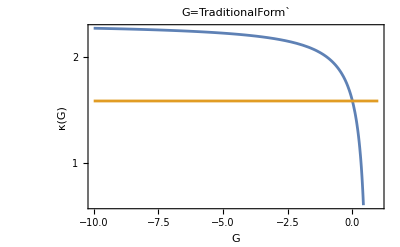

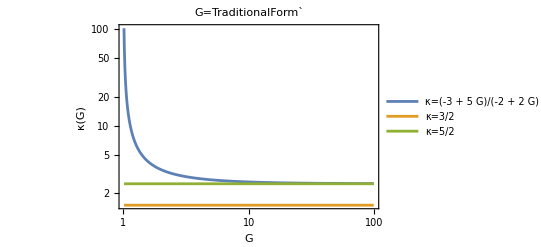

```mathematica
LogPlot[{(-3+5 G)/(-2+2 G),1.5},{G,-10,0.9999999},Frame->True,FrameLabel->{"G","κ(G)"}, PlotLabel->"G=TraditionalForm`"]
LogLogPlot[{(-3+5 G)/(-2+2 G),1.5,5/2},{G,1.01,100},Frame->True,FrameLabel->{"G","κ(G)"}, PlotLabel->"G=TraditionalForm`",PlotRange->All,PlotLegends->{"κ=(-3 + 5 G)/(-2 + 2 G)","κ=3/2","κ=5/2"}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]


(Subscript[n, c]/n *Subscript[T, c]^2+Subscript[n, h]/n*Subscript[T, h]^2)/(Subscript[n, c]/n*Subscript[T, c]+Subscript[n, h]/n*Subscript[T, h])^2//TraditionalForm
```

((n_c T_c^2)/n+(n_h T_h^2)/n)/((n_c T_c)/n+(n_h T_h)/n)^2

```mathematica
Expand[(nc Tc+nh Th)^2]
```

nc^2 Tc^2+2 nc nh Tc Th+nh^2 Th^2

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
n=nc+nh;
T=(nc/n*Tc+nh/n*Th)*(1-3/(2*κ));
(*H=(nc/n *Sqrt[Tc]+nh/n*Sqrt[Th])/Sqrt[nc/n*Tc+nh/n*Th];*)
(*assumps={Tc>0,Th>0,T>0,κ>5/2,nc>0,nh>0,m>0};*)
assumps={H>0,κ>3/2};
Solve[ H==(Sqrt[κ-3/2]*Gamma[κ-1])/Gamma[κ-1/2],κ,Assumptions->assumps]

Reduce[H>0&&κ>3/2&&H==(Sqrt[κ-3/2]*Gamma[κ-1])/Gamma[κ-1/2],κ,PositiveReals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[H==(√(-3/2+κ) Gamma[-1+κ])/Gamma[-1/2+κ],κ,Assumptions→{H>0,κ>3/2}]

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[H>0&&κ>3/2&&H==(√(-3/2+κ) Gamma[-1+κ])/Gamma[-1/2+κ],κ,]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
SetDirectory[]
(*n=nc+nh;
T=(nc/n*Tc+nh/n*Th)*(1-3/(2*κ));*)
(*H=(nc/n *Sqrt[Tc]+nh/n*Sqrt[Th])/Sqrt[nc/n*Tc+nh/n*Th];*)
assumps={Tc>0,Th>0,T>0,κ>3/2,nc>0,nh>0,m>0,n>0};
Solve[{T==(nc/n*Tc+nh/n*Th)*(1-3/(2*κ)),nc/n *Sqrt[Tc]+nh/n*Sqrt[Th] ==(Sqrt[T*κ]*Gamma[κ-1])/Gamma[κ-1/2]},{κ,T},Assumptions->assumps]

Reduce[{T==(nc/n*Tc+nh/n*Th)*(1-3/(2*κ)),nc/n *Sqrt[Tc]+nh/n*Sqrt[Th] ==(Sqrt[T*κ]*Gamma[κ-1])/Gamma[κ-1/2]},{κ,T},PositiveReals]
```

/Users/edne8319

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[{T==((nc Tc)/n+(nh Th)/n) (1-3/(2 κ)),(nc √Tc)/n+(nh √Th)/n==(√(T κ) Gamma[-1+κ])/Gamma[-1/2+κ]},{κ,T},Assumptions→{Tc>0,Th>0,T>0,κ>3/2,nc>0,nh>0,m>0,n>0}]

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{T==((nc Tc)/n+(nh Th)/n) (1-3/(2 κ)),(nc √Tc)/n+(nh √Th)/n==(√(T κ) Gamma[-1+κ])/Gamma[-1/2+κ]},{κ,T},]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
SetDirectory[]
(*n=nc+nh;
T=(nc/n*Tc+nh/n*Th)*(1-3/(2*κ));*)
(*α=(nc/n*Tc+nh/n*Th)*
β = nc/n *Sqrt[Tc]+nh/n*Sqrt[Th]*)
(*H=(nc/n *Sqrt[Tc]+nh/n*Sqrt[Th])/Sqrt[nc/n*Tc+nh/n*Th];*)
assumps={T>0,κ>3/2,α>0,β>0};
Solve[{T==α*(1-3/(2*κ)),β ==(Sqrt[T*κ]*Gamma[κ-1])/Gamma[κ-1/2]},{κ,T},Assumptions->assumps]

Reduce[{T==α*(1-3/(2*κ)),β ==(Sqrt[T*κ]*Gamma[κ-1])/Gamma[κ-1/2]},{κ,T},PositiveReals]
```